All sections can be opened by mouse-click.

### Overview of Approach

Task 1.1

Using normalized data, searched through all features to add to the IgG_PT pre-vac feature, checking for how well each one improves predictions against all IgG features (to check for robustness)

Going from 2020+2021→2022, only YearsSinceVaccination and two other Ab features improved results slightly. None of the antibody features ended up making better predictions in 2022

Final model uses IgG_PT and YearsSince Vaccination through a Random Forest model

Checked how best to combine the results from 2020-2022 (testing on {2020,2021}→2022, {2020,2022}→2021, {2022,2021}→2020). Taking the arithmetic average of the predictions from each year, and then taking the ranking of the result, worked best

In the final model, 2021 ended up making flat predictions, so that neither helps nor hurts the model. So basically 2020 and 2022 contribute to the final predictions. There are lots of ties, and I let Mathematica order them arbitrarily, since this will likely minimally effect the result

Task 1.2

Raw data works better than normalized data

Surprisingly, could not find any feature that worked consistently better than 1/(day 0), so went with this baseline model (which was the winning model in the 2nd challenge)

Task 2.1

Similar to task 1.1, looked for features that robustly improved predictions across all cell type features

Baseline already does well, so it is easy to build up upon it

Task 2.2

Note that a null model (using baseline only) does poorly, making this a much harder challenge

Used batch-corrected data, with the first feature being “Proliferating B cells,” since it had the best correlation with Monocyte fold-change

It is difficult to decide which other features are good, since averaging across all cell type features does very poorly. Ended up picking out the best 7 features that were well-predicted by Proliferating B cells, hoping that this set would still give me some measure of robustness

No other feature helped, but Monocytes didn’t make things worse, so that was added back for safety

Task 3.1

Unclear how to do a robust search with so many genes, so went with the simple (and mediocre) model of using the baseline gene expression for that gene

Task 3.2

No team did well on this last year, so this task may be impossible

Looked for which features had the best correlation with the gene-of-interest’s fold-change. Top hits were “IgG2_FHA” and “IgG2_DT”, although neither did well in 2020 (but both were good in 2021-2022). Ended up using “IgG2_FHA”

Task 4.1

Baseline was good, but there were also plenty of other features that robustly made all T cell polarization features better (not looking at their ratios, just predicting each one outright)

Chose the single best predictive parameter (“CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells”) and used it in a random forest model together with the baseline parameter (ratio of the two features of interest)

Trying to use all data (including demographics and other modalities), but requiring the resulting model to be robustly better against all Ab/T cell features

Only using Day 0. Only 2022 and 2023 have Days -30 and -14, which are ignored

Predicting across every possible pair of studies (2020→2021 and 2021→2020 for training, 2020+2021→2022, 2021+2022→2020, 2022+2020→2021 for validation). We can compute Spearman’s coefficient and average the two results

## Task 1

Goal: Predict IgG MFI against pertussis toxin (PT) at Day 14

### Task 1.1: Absolute PT IgG Titer

#### Potential pitfall

Classic example of why it may seem like adding another feature slightly improves predictions, but it turns out to knock you out in 2022

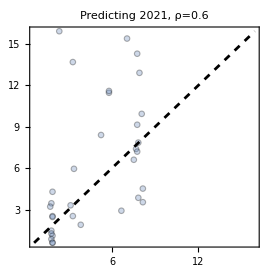
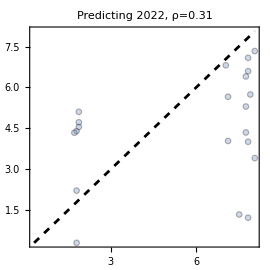

```mathematica
featureOfInterest="IgG_PT";
Table[
features={"IgG_PT","IgG2_DT"};
predict=Predict[Cases[Table[assocSubjectAbDay0[{#,feature}],{feature,features}]->assocSubjectAbPost[{#,featureOfInterest}]&/@sera[2020],HoldPattern[{_?NumericQ..}->_?NumericQ]],TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocSubjectAbDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{_?NumericQ..}],
predict[input],
Missing[]
],assocSubjectAbPost[{#,featureOfInterest}]}&/@sera[yearToPredict],{_?NumericQ..}];
plot[plotData,PlotLabel->Row[{"Predicting ",yearToPredict,", ρ=",Round[SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData],0.01]}]]
,{yearToPredict,{2021,2022}}]
```

#### Testing, Searching through all features to add to Baseline

Goal:

Which other features leads to consistently better predictions against ever antibody (Ab) feature?

After we add all such features (perhaps testing their combinations), make the final model to predict the 2022 results, and see whether this model actually does better than the base model (just using the baseline of the feature of interest)

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listAbFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectAbPost[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectAbPost[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{}]
resBase[2021,2020]=analyze[2021,2020,{}]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.59298,0.143733,-0.671713,-0.474731,0.395198,0.755759,-0.373656,0.406886,0.478516,0.741226,0.821937,0.677058,0.835264,0.293689,0.524677,0.857043,0.971284,0.653386,0.523729,0.451324,0.506928,0.773597,0.828042,0.948286,0.761632,0.683863,0.870733,0.511917,0.92224,0.888974,0.937849}

{0.254904,0.290023,Indeterminate,0.536751,0.438383,0.470937,-0.0237595,0.512298,0.434954,0.829469,0.614775,0.615048,0.635689,0.319258,0.635934,0.878278,0.969942,0.223383,0.495858,0.480476,0.491814,0.368198,0.796794,0.856893,0.697389,0.777598,0.836909,Indeterminate,0.838673,0.8059,0.884507}

⟨ρ⟩=  0.57

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2020,2021,newFeature]=analyze[2020,2021,newFeature];
resFeature[2021,2020,newFeature]=analyze[2021,2020,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2020,2021],resBase[2021,2020]],Join[resFeature[2020,2021,newFeature],resFeature[2021,2020,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,List/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]]}]
```

On:  {VacType}

{ρ_base,ρ_new}  {0.57,0.5}

On:  {Sex}

{ρ_base,ρ_new}  {0.57,0.51}

On:  {Age}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {YearsSinceBoost}

{ρ_base,ρ_new}  {0.57,0.58}

On:  {IgG_PT}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG_PRN}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG_FHA}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG1_PT}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {IgG1_PRN}

{ρ_base,ρ_new}  {0.57,0.52}

On:  {IgG1_FHA}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG1_FIM2/3}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG1_TT}

{ρ_base,ρ_new}  {0.57,0.58}

On:  {IgG1_DT}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG1_OVA}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG2_PT}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG2_PRN}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG2_FHA}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG2_FIM2/3}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG2_TT}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG2_DT}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG3_PT}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG3_PRN}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG3_FHA}

{ρ_base,ρ_new}  {0.57,0.57}

On:  {IgG3_FIM2/3}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG3_TT}

{ρ_base,ρ_new}  {0.57,0.57}

On:  {IgG3_DT}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG3_OVA}

{ρ_base,ρ_new}  {0.57,0.54}

On:  {IgG4_PT}

{ρ_base,ρ_new}  {0.57,0.57}

On:  {IgG4_PRN}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG4_FHA}

{ρ_base,ρ_new}  {0.57,0.55}

On:  {IgG4_FIM2/3}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG4_TT}

{ρ_base,ρ_new}  {0.57,0.56}

On:  {IgG4_DT}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {IgG4_OVA}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {P05231}

{ρ_base,ρ_new}  {0.57,0.49}

On:  {P51671}

{ρ_base,ρ_new}  {0.57,0.52}

On:  {P22301}

{ρ_base,ρ_new}  {0.57,0.5}

On:  {P48061}

{ρ_base,ρ_new}  {0.59,0.52}

On:  {P10145}

{ρ_base,ρ_new}  {0.57,0.5}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.57,0.53}

On:  {Classical_Monocytes}

{ρ_base,ρ_new}  {0.57,0.52}

On:  {Non-Classical_Monocytes}

{ρ_base,ρ_new}  {0.57,0.49}

On:  {Intermediate_Monocytes}

{ρ_base,ρ_new}  {0.57,0.5}

On:  {Bcells}

{ρ_base,ρ_new}  {0.57,0.54}

```mathematica
(* Cases where an additional feature seems to help *)
Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]],entry_/;entry[[-1]]>=entry[[-2]]]
```

{{YearsSinceBoost,0.570082,0.583162},{IgG1_TT,0.570082,0.575098},{IgG3_FHA,0.570082,0.571892}}

Did these features work?

YearsSinceBoost did make things slightly better...the two antibody features did not

Combinations of features were not reliable either

```mathematica
testFeature="YearsSinceBoost"(*"IgG1_TT"*)(*"IgG3_FHA"*);
(* Confirming expected improvement *)
analyze[2020,2021,#,{"IgG_PT"}]&/@{{},{testFeature}}
analyze[2021,2020,#,{"IgG_PT"}]&/@{{},{testFeature}}
(* Testing on 2022 *)
analyze[2020,2022,#,{"IgG_PT"}]&/@{{},{testFeature}}
analyze[2021,2022,#,{"IgG_PT"}]&/@{{},{testFeature}}
```

{{0.59298},{0.639114}}

{{0.254904},{0.314982}}

{{0.476749},{0.477759}}

{{0.267488},{0.326393}}

```mathematica
testFeature={"YearsSinceBoost",(*"IgG1_TT"*)"IgG3_FHA"};
(* Confirming expected improvement *)
analyze[2020,2021,#,{"IgG_PT"}]&/@{{},testFeature}
analyze[2021,2020,#,{"IgG_PT"}]&/@{{},testFeature}
(* Testing on 2022 *)
analyze[2020,2022,#,{"IgG_PT"}]&/@{{},testFeature}
analyze[2021,2022,#,{"IgG_PT"}]&/@{{},testFeature}
```

{{0.59298},{0.609886}}

{{0.254904},{0.333268}}

{{0.476749},{0.236973}}

{{0.267488},{0.166596}}

Testing YearsSinceBoost in all directions with 2022
Conclusions: it is consistent enough that I would use it!

```mathematica
analyze[2020,2021,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
analyze[2020,2022,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
analyze[2021,2020,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
analyze[2021,2022,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
analyze[2022,2020,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
analyze[2022,2021,#,{"IgG_PT"}]&/@{{},{"YearsSinceBoost"}}
```

{{0.59298},{0.639114}}

{{0.476749},{0.477759}}

{{0.254904},{0.314982}}

{{0.267488},{0.326393}}

{{0.495969},{0.522733}}

{{0.633137},{0.561385}}

#### Combining results: Using “IgG_PT” and “YearSinceVaccination”

How should we combine the results?

[Winner] Take the mean of each year’s predictions

Take the average of the rankings

Combine all of the training years together and then predict

```mathematica
Clear[combine]
combine[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listAbFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectAbPost[{#,featureOfInterest}]&/@Join@@sera/@Flatten@List@yearTraining,HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectAbPost[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
{First@Transpose@plotData,Last@Transpose@plotData}
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
train1[1]=combine[2020,2021,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train2[1]=combine[2022,2021,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train1And2[1]=combine[{2020,2022},2021,{"YearsSinceBoost"},listAbFeatures[[;;]]];
```

```mathematica
train1[2]=combine[2020,2022,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train2[2]=combine[2021,2022,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train1And2[2]=combine[{2020,2021},2022,{"YearsSinceBoost"},listAbFeatures[[;;]]];
```

```mathematica
train1[3]=combine[2021,2020,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train2[3]=combine[2022,2020,{"YearsSinceBoost"},listAbFeatures[[;;]]];
train1And2[3]=combine[{2021,2022},2020,{"YearsSinceBoost"},listAbFeatures[[;;]]];
```

```mathematica
Table[
Mean@DeleteMissing@Table[
If[MemberQ[{3,21,25,28},jj],
Missing[],
SpearmanRho[Mean/@Transpose@{train1[kk][[jj,1]],train2[kk][[jj,1]]},train1[kk][[jj,2]]]
]
,{jj,Length@train1[kk]}]
,{kk,3}]
```

{0.66876,0.747768,0.603301}

Take the average of the rankings

```mathematica
Table[
Mean@DeleteMissing@Table[
If[MemberQ[{3,21,25,28},jj],
Missing[],
rnks=Ordering[Ordering[#]]&/@{train1[kk][[jj,1]],train1[kk][[jj,2]]};
rnks2=Ordering[Ordering[#]]&/@{train2[kk][[jj,1]],train2[kk][[jj,2]]};
Correlation[Mean[{rnks⟦1⟧,rnks2⟦1⟧}],rnks2⟦2⟧]//N
]
,{jj,Length@train1[kk]}]
,{kk,3}]
```

{0.647751,0.70566,0.569292}

Can combine all of the training years together and then predict

```mathematica
Mean[SpearmanRho[#[[1]],#[[2]]]&/@train1And2[1]]
Mean[SpearmanRho[#[[1]],#[[2]]]&/@train1And2[2]]
Mean[SpearmanRho[#[[1]],#[[2]]]&/@train1And2[3]]
```

0.572646

0.712583

0.542901

#### Final Model: Using “IgG_PT” and “YearSinceVaccination”

Use “IgG_PT” and “YearSinceVaccination” as input variables

Take the mean of each year’s predictions

```mathematica
Clear[combine]
combine[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listAbFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectAbPost[{#,featureOfInterest}]&/@Join@@sera/@Flatten@List@yearTraining,HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],0(*assocSubjectAbPost[{#,featureOfInterest}]*)}&/@sera[yearTesting],{_?NumericQ..}];
{First@Transpose@plotData,Last@Transpose@plotData}
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
res2020=combine[2020,2023,{"YearsSinceBoost"},listAbFeatures[[{1}]]]
res2021=combine[2021,2023,{"YearsSinceBoost"},listAbFeatures[[{1}]]]
res2022=combine[2022,2023,{"YearsSinceBoost"},listAbFeatures[[{1}]]]
```

{{{8.53457,8.53457,8.45621,8.6913,8.6913,8.45621,8.53457,8.6913,8.45621,8.53457,8.45621,8.53457,8.45621,8.53457,8.53457,7.35911,8.45621,8.45621,8.45621,8.53457,8.45621,8.45621,8.6913,7.35911,8.53457,8.6913,7.04566,8.6913,8.6913,8.61294,8.6913,8.6913,7.04566,8.53457,8.61294,7.35911,8.6913,8.6913,8.53457,8.6913,8.61294,8.6913,8.53457,8.53457,6.96729,8.61294,8.53457,8.45621,6.88893,8.6913,8.45621,8.45621,8.45621,8.61294},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{{{5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755,5.755},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

{{{5.59656,5.59656,4.56014,5.59656,5.71171,4.56014,4.75207,4.75207,4.56014,4.98239,4.56014,4.98239,4.56014,5.59656,4.98239,4.4066,4.56014,4.56014,4.56014,5.59656,4.56014,4.56014,4.75207,3.56212,4.21467,5.13593,3.56212,5.2127,5.2127,3.90759,5.2127,5.09754,3.6005,5.09754,3.90759,3.6005,3.90759,5.05916,5.09754,5.05916,3.90759,5.2127,5.09754,3.90759,3.6005,5.09754,3.90759,3.67728,3.6005,5.2127,3.67728,3.67728,3.67728,4.75207},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

The 2021 data clearly has no impact, since it predicted the same value everywhere. Including it anyways, since it won’t affect anything

```mathematica
predictTask[1.1]=Mean/@Transpose@{res2020[[1,1]],res2021[[1,1]],res2022[[1,1]]}
```

{6.62871,6.62871,6.25712,6.68095,6.71934,6.25712,6.34722,6.39946,6.25712,6.42399,6.25712,6.42399,6.25712,6.62871,6.42399,5.84024,6.25712,6.25712,6.25712,6.62871,6.25712,6.25712,6.39946,5.55875,6.16808,6.52741,5.45426,6.553,6.553,6.09184,6.553,6.51462,5.46706,6.46237,6.09184,5.57154,6.11796,6.50182,6.46237,6.50182,6.09184,6.553,6.46237,6.06572,5.44093,6.48849,6.06572,5.96283,5.41481,6.553,5.96283,5.96283,5.96283,6.37334}

```mathematica
predictTask[1.1]={6.628710961948179,6.628710961948179,6.257119132366391,6.680953566001943,6.7193391801747095,6.257119132366391,6.34721645801455,6.399459062068314,6.257119132366391,6.4239876863600855,6.257119132366391,6.4239876863600855,6.257119132366391,6.628710961948179,6.4239876863600855,5.840240085093022,6.257119132366391,6.257119132366391,6.257119132366391,6.628710961948179,6.257119132366391,6.257119132366391,6.399459062068314,5.558745581159395,6.168083591874971,6.527411109310873,5.454260373051867,6.553001518759385,6.553001518759385,6.091843256107805,6.553001518759385,6.514615904586617,5.467055577776123,6.462373300532853,6.091843256107805,5.571540785883651,6.1179645581346875,6.501820699862361,6.462373300532853,6.501820699862361,6.091843256107805,6.553001518759385,6.462373300532853,6.0657219540809235,5.4409342757492425,6.488494602559736,6.0657219540809235,5.962829423708508,5.41481297372236,6.553001518759385,5.962829423708508,5.962829423708508,5.962829423708508,6.373337760041433};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[1.1]]
```

{3,4,27,2,1,28,26,23,29,20,30,21,31,5,22,48,32,33,34,6,35,36,24,50,37,12,52,7,8,39,9,13,51,17,40,49,38,14,18,15,41,10,19,42,53,16,43,44,54,11,45,46,47,25}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,5]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 |  |  |  |  |  | 
120 | 27 | Female | wP | 4 |  |  |  |  |  | 
121 | 22 | Female | aP | 27 |  |  |  |  |  | 
122 | 23 | Female | aP | 2 |  |  |  |  |  | 
123 | 26 | Female | wP | 1 |  |  |  |  |  | 
124 | 22 | Male | aP | 28 |  |  |  |  |  | 
125 | 29 | Male | wP | 26 |  |  |  |  |  | 
126 | 29 | Male | wP | 23 |  |  |  |  |  | 
127 | 26 | Female | aP | 29 |  |  |  |  |  | 
128 | 28 | Female | wP | 20 |  |  |  |  |  | 
129 | 31 | Male | wP | 30 |  |  |  |  |  | 
130 | 26 | Male | wP | 21 |  |  |  |  |  | 
131 | 24 | Female | aP | 31 |  |  |  |  |  | 
132 | 27 | Male | wP | 5 |  |  |  |  |  | 
133 | 25 | Female | aP | 22 |  |  |  |  |  | 
134 | 32 | Male | wP | 48 |  |  |  |  |  | 
135 | 27 | Male | wP | 32 |  |  |  |  |  | 
136 | 27 | Female | wP | 33 |  |  |  |  |  | 
137 | 24 | Female | aP | 34 |  |  |  |  |  | 
138 | 22 | Male | aP | 6 |  |  |  |  |  | 
139 | 29 | Female | wP | 35 |  |  |  |  |  | 
140 | 21 | Female | aP | 36 |  |  |  |  |  | 
141 | 26 | Female | wP | 24 |  |  |  |  |  | 
142 | 31 | Female | aP | 50 |  |  |  |  |  | 
143 | 19 | Female | aP | 37 |  |  |  |  |  | 
144 | 23 | Female | aP | 12 |  |  |  |  |  | 
145 | 20 | Male | aP | 52 |  |  |  |  |  | 
146 | 31 | Male | wP | 7 |  |  |  |  |  | 
147 | 23 | Female | aP | 8 |  |  |  |  |  | 
148 | 35 | Male | wP | 39 |  |  |  |  |  | 
149 | 32 | Female | wP | 9 |  |  |  |  |  | 
150 | 32 | Male | wP | 13 |  |  |  |  |  | 
151 | 31 | Female | wP | 51 |  |  |  |  |  | 
152 | 28 | Female | wP | 17 |  |  |  |  |  | 
153 | 25 | Female | aP | 40 |  |  |  |  |  | 
154 | 26 | Female | aP | 49 |  |  |  |  |  | 
155 | 26 | Female | aP | 38 |  |  |  |  |  | 
156 | 22 | Female | aP | 14 |  |  |  |  |  | 
157 | 26 | Female | aP | 18 |  |  |  |  |  | 
158 | 23 | Male | aP | 15 |  |  |  |  |  | 
159 | 29 | Female | wP | 41 |  |  |  |  |  | 
160 | 27 | Male | aP | 10 |  |  |  |  |  | 
161 | 30 | Female | aP | 19 |  |  |  |  |  | 
162 | 24 | Female | aP | 42 |  |  |  |  |  | 
163 | 30 | Female | wP | 53 |  |  |  |  |  | 
164 | 32 | Male | wP | 16 |  |  |  |  |  | 
165 | 30 | Female | wP | 43 |  |  |  |  |  | 
166 | 22 | Female | aP | 44 |  |  |  |  |  | 
167 | 26 | Male | aP | 54 |  |  |  |  |  | 
168 | 32 | Male | wP | 11 |  |  |  |  |  | 
169 | 20 | Male | aP | 45 |  |  |  |  |  | 
170 | 31 | Male | wP | 46 |  |  |  |  |  | 
171 | 20 | Female | wP | 47 |  |  |  |  |  | 
172 | 36 | Male | wP | 25 |  |  |  |  |  |

### Task 1.2: Fold Change of PT IgG Titer

#### Batch Correction does not help in this task

It appears to be a mistake to use batch corrected data. Using raw data instead

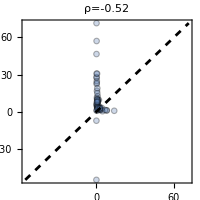
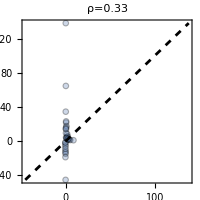
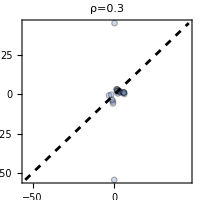

```mathematica
(* Using batch-corrected data *)
Table[
plotData=Cases[{assocSubjectAbDay0[{#,"IgG_PT"}],assocSubjectAbPost[{#,"IgG_PT"}]/assocSubjectAbDay0[{#,"IgG_PT"}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}]],{year,2020,2022}]
```

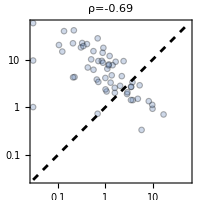
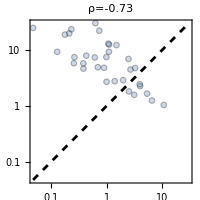
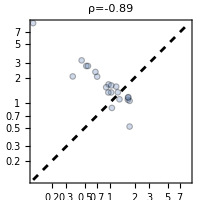

```mathematica
(* Using raw data *)
Table[
plotData=Cases[{assocSubjectAbDay0Raw[{#,"IgG_PT"}],assocSubjectAbPostRaw[{#,"IgG_PT"}]/assocSubjectAbDay0Raw[{#,"IgG_PT"}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

#### Testing, Searching through all features to add to Baseline

Do any other features leads to consistently better predictions against all Ab features?

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listAbFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0Raw[{#,feature}],{feature,features}]->assocSubjectAbPostRaw[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0Raw[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectAbPostRaw[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{}]
resBase[2021,2020]=analyze[2021,2020,{}]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.654202,-0.157919,-0.82823,0.469987,0.399937,0.614882,-0.259175,0.383005,0.527587,0.536132,0.847832,0.682115,0.883494,0.478946,0.708846,0.84109,0.982215,0.559363,0.656286,0.568438,0.684785,0.580877,0.873891,0.764272,0.859345,0.792754,0.929298,0.622377,0.956948,0.87653,0.94529}

{0.425905,0.0618709,0.0295398,0.694583,0.43571,0.375351,-0.0626704,0.526604,0.403889,0.875044,0.732964,0.619046,0.634486,0.467244,0.63445,0.957763,0.970157,0.409165,0.490127,0.471505,0.598159,0.444857,0.7786,0.834847,0.780229,0.766979,0.840355,0.35015,0.857383,0.807952,0.90027}

⟨ρ⟩=  0.59

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2020,2021,newFeature]=analyze[2020,2021,newFeature];
resFeature[2021,2020,newFeature]=analyze[2021,2020,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2020,2021],resBase[2021,2020]],Join[resFeature[2020,2021,newFeature],resFeature[2021,2020,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,List/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]]}]
```

On:  {VacType}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Sex}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Age}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {YearsSinceBoost}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG_PT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG_PRN}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG_FHA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG1_PT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_PRN}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_FHA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG1_TT}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG1_DT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG1_OVA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_PT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_PRN}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG2_FHA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG2_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG2_TT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG2_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG3_PT}

{ρ_base,ρ_new}  {0.59,0.59}

On:  {IgG3_PRN}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG3_FHA}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_TT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG3_OVA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_PT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG4_PRN}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_FHA}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG4_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.59}

On:  {IgG4_TT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG4_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_OVA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {P05231}

{ρ_base,ρ_new}  {0.59,0.54}

On:  {P51671}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {P22301}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {P48061}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {P10145}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Classical_Monocytes}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Non-Classical_Monocytes}

{ρ_base,ρ_new}  {0.59,0.53}

On:  {Intermediate_Monocytes}

{ρ_base,ρ_new}  {0.59,0.53}

On:  {Bcells}

{ρ_base,ρ_new}  {0.59,0.58}

```mathematica
(* Cases where an additional feature seems to help *)
Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]],entry_/;entry[[-1]]>=entry[[-2]]]
```

{{YearsSinceBoost,0.589482,0.599505},{IgG1_FIM2/3,0.589482,0.600876},{IgG1_TT,0.589482,0.595514},{IgG3_PT,0.589482,0.591056}}

#### Comparing Baseline + Extra

Conclusion: Surprisingly, this did not find any features that do better than 1/day0 in terms of predicting the rank correlation consistently across all Ab features

```mathematica
Echo[Mean/@Table[
SpearmanRho@@Transpose@Cases[Transpose@{-assocSubjectAbDay0Raw[{#,feature}]&/@sera[year],assocSubjectAbPostRaw[{#,feature}]/(assocSubjectAbDay0Raw[{#,feature}]+$MachineEpsilon)&/@sera[year]},{_?NumericQ..}]
,{year,2020,2022},{feature,listAbFeatures[[{1}]]}],"IgG_PA Only"];
Echo[Mean/@Table[
SpearmanRho@@Transpose@Cases[Transpose@{-assocSubjectAbDay0Raw[{#,feature}]&/@sera[year],assocSubjectAbPostRaw[{#,feature}]/(assocSubjectAbDay0Raw[{#,feature}]+$MachineEpsilon)&/@sera[year]},{_?NumericQ..}]
,{year,2020,2022},{feature,listAbFeatures}],"All Ab features"];
```

IgG_PA Only  {0.692746,0.728944,0.888312}

All Ab features  {0.398174,0.363551,0.410219}

#### Final Model: Using baseline “IgG_PT”

```mathematica
predictTask[1.2]=1/assocSubjectAbDay0Raw[{#,"IgG_PT"}]&/@sera[2023]
MinMax[1/assocSubjectAbDay0Raw[{#,"IgG_PT"}]&/@sera[2023]]
```

{0.63968,0.662556,1.36806,0.533394,0.449772,1.62363,0.985,1.00169,1.50765,0.884731,1.40714,0.854046,1.58871,0.659598,0.856522,2.23864,1.67898,1.38732,1.38084,0.753827,1.43447,1.36806,1.03322,2.34524,0.861516,0.0885791,2.73611,0.0728371,0.269617,1.15595,0.235646,0.518421,2.66296,0.800668,1.25212,2.1413,1.06994,0.497922,0.720441,0.496547,1.17484,0.18598,0.820776,0.969003,3.66837,0.625217,0.96123,1.47336,3.20982,0.426453,1.8724,1.41535,1.66435,1.25261}

{0.0728371,3.66837}

```mathematica
predictTask[1.2]={0.6396797153024917,0.6625560538116575,1.3680555555555558,0.5333935018050553,0.44977168949771623,1.623626373626373,0.9849999999999992,1.0016949152542367,1.5076530612244887,0.8847305389221523,1.4071428571428577,0.8540462427745686,1.5887096774193554,0.6595982142857153,0.8565217391304348,2.2386363636363646,1.6789772727272725,1.3873239436619713,1.380841121495327,0.7538265306122433,1.4344660194174754,1.3680555555555558,1.0332167832167836,2.3452380952380976,0.8615160349854255,0.08857913669064782,2.7361111111111116,0.07283707172787801,0.2696167883211679,1.155948553054663,0.23564593301435383,0.5184210526315801,2.6629629629629648,0.8006681514476625,1.2521186440677963,2.141304347826087,1.0699404761904758,0.49792243767312966,0.720440881763525,0.496546961325966,1.1748366013071894,0.18598034143817896,0.8207762557077621,0.9690026954177868,3.6683673469387683,0.6252173913043486,0.9612299465240686,1.4733606557377048,3.209821428571434,0.42645314353499447,1.8723958333333326,1.4153543307086611,1.6643518518518512,1.2526132404181192};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[1.2]]
```

{42,40,20,44,48,11,29,28,13,32,17,35,12,41,34,6,9,18,19,38,15,21,27,5,33,53,3,54,50,25,51,45,4,37,23,7,26,46,39,47,24,52,36,30,1,43,31,14,2,49,8,16,10,22}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,6]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 |  |  |  |  | 
120 | 27 | Female | wP | 4 | 40 |  |  |  |  | 
121 | 22 | Female | aP | 27 | 20 |  |  |  |  | 
122 | 23 | Female | aP | 2 | 44 |  |  |  |  | 
123 | 26 | Female | wP | 1 | 48 |  |  |  |  | 
124 | 22 | Male | aP | 28 | 11 |  |  |  |  | 
125 | 29 | Male | wP | 26 | 29 |  |  |  |  | 
126 | 29 | Male | wP | 23 | 28 |  |  |  |  | 
127 | 26 | Female | aP | 29 | 13 |  |  |  |  | 
128 | 28 | Female | wP | 20 | 32 |  |  |  |  | 
129 | 31 | Male | wP | 30 | 17 |  |  |  |  | 
130 | 26 | Male | wP | 21 | 35 |  |  |  |  | 
131 | 24 | Female | aP | 31 | 12 |  |  |  |  | 
132 | 27 | Male | wP | 5 | 41 |  |  |  |  | 
133 | 25 | Female | aP | 22 | 34 |  |  |  |  | 
134 | 32 | Male | wP | 48 | 6 |  |  |  |  | 
135 | 27 | Male | wP | 32 | 9 |  |  |  |  | 
136 | 27 | Female | wP | 33 | 18 |  |  |  |  | 
137 | 24 | Female | aP | 34 | 19 |  |  |  |  | 
138 | 22 | Male | aP | 6 | 38 |  |  |  |  | 
139 | 29 | Female | wP | 35 | 15 |  |  |  |  | 
140 | 21 | Female | aP | 36 | 21 |  |  |  |  | 
141 | 26 | Female | wP | 24 | 27 |  |  |  |  | 
142 | 31 | Female | aP | 50 | 5 |  |  |  |  | 
143 | 19 | Female | aP | 37 | 33 |  |  |  |  | 
144 | 23 | Female | aP | 12 | 53 |  |  |  |  | 
145 | 20 | Male | aP | 52 | 3 |  |  |  |  | 
146 | 31 | Male | wP | 7 | 54 |  |  |  |  | 
147 | 23 | Female | aP | 8 | 50 |  |  |  |  | 
148 | 35 | Male | wP | 39 | 25 |  |  |  |  | 
149 | 32 | Female | wP | 9 | 51 |  |  |  |  | 
150 | 32 | Male | wP | 13 | 45 |  |  |  |  | 
151 | 31 | Female | wP | 51 | 4 |  |  |  |  | 
152 | 28 | Female | wP | 17 | 37 |  |  |  |  | 
153 | 25 | Female | aP | 40 | 23 |  |  |  |  | 
154 | 26 | Female | aP | 49 | 7 |  |  |  |  | 
155 | 26 | Female | aP | 38 | 26 |  |  |  |  | 
156 | 22 | Female | aP | 14 | 46 |  |  |  |  | 
157 | 26 | Female | aP | 18 | 39 |  |  |  |  | 
158 | 23 | Male | aP | 15 | 47 |  |  |  |  | 
159 | 29 | Female | wP | 41 | 24 |  |  |  |  | 
160 | 27 | Male | aP | 10 | 52 |  |  |  |  | 
161 | 30 | Female | aP | 19 | 36 |  |  |  |  | 
162 | 24 | Female | aP | 42 | 30 |  |  |  |  | 
163 | 30 | Female | wP | 53 | 1 |  |  |  |  | 
164 | 32 | Male | wP | 16 | 43 |  |  |  |  | 
165 | 30 | Female | wP | 43 | 31 |  |  |  |  | 
166 | 22 | Female | aP | 44 | 14 |  |  |  |  | 
167 | 26 | Male | aP | 54 | 2 |  |  |  |  | 
168 | 32 | Male | wP | 11 | 49 |  |  |  |  | 
169 | 20 | Male | aP | 45 | 8 |  |  |  |  | 
170 | 31 | Male | wP | 46 | 16 |  |  |  |  | 
171 | 20 | Female | wP | 47 | 10 |  |  |  |  | 
172 | 36 | Male | wP | 25 | 22 |  |  |  |  |

## Task 2

Goal: Predict % live cells for Monocytes in the pbmc_cell_frequency files

### Task 2.1

#### Using Baseline alone

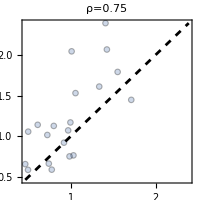
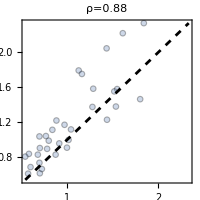
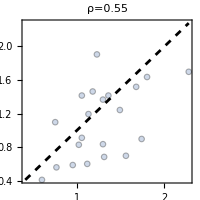

```mathematica
Table[
plotData=DeleteMissing[Transpose@{assocDay0/@({#,"Monocytes"}&/@sera[year]),assocSubjectCellFrequencyPost/@({#,"Monocytes"}&/@sera[year])},1,All];
plot[plotData,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ImageSize->200]
,{year,2020,2022}]
```

Conclusion: Using baseline is an excellent (and consistent!) good predictor of a feature’s post-vac value

```mathematica
(* ρ for every feature in 2020-2022 *)
Table[
plotData=DeleteMissing[Transpose@{assocDay0/@({#,feature}&/@sera[year]),assocSubjectCellFrequencyPost/@({#,feature}&/@sera[year])},1,All];
SpearmanRho[First/@plotData,Last/@plotData]
,{feature,listCellFrequencyFeatures[[;;]]},{year,2020,2022}]
```

{{0.750376,0.875888,0.551511},{0.670677,0.868366,0.506173},{0.821361,0.850932,0.464587},{0.59768,0.750711,0.80793},{0.690226,0.799331,0.612086},{0.801504,0.871658,0.771429},{0.723308,0.87756,0.746996},{0.747368,0.916339,0.826511},{0.843609,0.955541,0.840156},{0.645974,0.9053,0.897986},{0.744361,0.881424,0.912931},{0.73985,0.833751,0.737252},{0.390977,0.918756,0.836364},{0.828571,0.956885,0.857143},{0.621053,0.947351,0.809354},{0.503759,0.891693,0.942514},{0.741353,0.738251,0.918348},{0.595489,0.779004,0.48668},{0.407519,0.791238,0.480988},{0.475188,0.858767,0.760339},{0.637594,0.811184,0.602664},{0.637594,0.808107,0.623377},{0.753383,0.909334,0.674894},{0.637594,0.867101,0.812602},{0.718797,0.954933,0.81053},{0.601504,0.948319,0.777163},{0.696241,0.848424,0.646524},{0.705263,0.756433,0.851309},{0.637594,0.956456,0.813515},{0.664662,0.74812,0.495127},{0.790977,0.883503,0.594998},{0.603008,0.787321,0.547287},{0.598496,0.84562,0.813802},{0.603008,0.811904,0.576448},{0.595489,0.812186,0.730834},{0.603008,0.78052,0.59987},{0.693233,0.821838,0.880915},{0.72782,0.904137,0.924326},{0.819549,0.852354,0.722692}}

#### Testing, Searching through all features to add to Baseline

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listCellFrequencyFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectCellFrequencyPost[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectCellFrequencyPost[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{}]
resBase[2021,2020]=analyze[2021,2020,{}]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.857589,0.815331,0.746906,0.568095,0.741661,0.859488,0.874802,0.896213,0.927602,0.925409,0.868309,0.829569,0.897858,0.951827,0.907253,0.872173,0.736222,0.735595,0.783626,0.850718,0.813705,0.803784,0.902402,0.831226,0.92774,0.694922,0.868898,0.602737,0.940591,0.238082,0.864974,0.734341,0.839469,0.793438,0.669712,0.782136,0.653834,0.660666,0.821129}

{0.734427,0.589878,0.841398,0.60222,0.66935,0.785629,0.720439,0.74873,0.853433,0.662581,0.735485,0.749308,0.395668,0.757113,0.599772,0.463059,0.759903,0.592662,0.449882,0.448774,0.681192,0.681192,0.651228,0.651206,0.684689,0.589476,0.686909,0.651353,0.650957,0.656062,0.802878,0.608726,0.621855,0.592511,0.597363,0.605182,0.719327,0.626741,0.843949}

⟨ρ⟩=  0.73

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2020,2021,newFeature]=analyze[2020,2021,newFeature];
resFeature[2021,2020,newFeature]=analyze[2021,2020,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2020,2021],resBase[2021,2020]],Join[resFeature[2020,2021,newFeature],resFeature[2021,2020,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,(List/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]]])}]
```

On:  {VacType}

{ρ_base,ρ_new}  {0.73,0.68}

On:  {Sex}

{ρ_base,ρ_new}  {0.73,0.67}

On:  {Age}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {YearsSinceBoost}

{ρ_base,ρ_new}  {0.73,0.74}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {Classical_Monocytes}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {Non-Classical_Monocytes}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Intermediate_Monocytes}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {Bcells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {CD3CD19neg}

{ρ_base,ρ_new}  {0.73,0.67}

On:  {CD3 Tcells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {CD4Tcells}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {CD8Tcells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {TemraCD4}

{ρ_base,ρ_new}  {0.73,0.73}

On:  {NaiveCD4}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {TemCD4}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {TcmCD4}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {TemraCD8}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {NaiveCD8}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {TemCD8}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {TcmCD8}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {NK}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Basophils}

{ρ_base,ρ_new}  {0.73,0.68}

On:  {pDC}

{ρ_base,ρ_new}  {0.73,0.68}

On:  {B cells (CD19+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {B cells (CD19+CD20+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {Memory B cells}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {Naive B cells}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Proliferating B cells}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Activated B cells (ABCs)}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {CD56+CD3+T cells}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {CD4+CD8+ T cells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {CD4-CD8- T cells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {NK cells (CD3-CD19-CD56+)}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {CD3-CD19-CD56- cells}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {non-pDCs}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {Conventional dendritic cells (cDCs)}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {cDC1}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {cDC2}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Activated granulocytes}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-)}

{ρ_base,ρ_new}  {0.73,0.68}

On:  {CD56high NK cells}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG_PT}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {IgG_PRN}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG_FHA}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {IgG1_PT}

{ρ_base,ρ_new}  {0.73,0.73}

On:  {IgG1_PRN}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG1_FHA}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG1_FIM2/3}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG1_TT}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG1_DT}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG1_OVA}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG2_PT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG2_PRN}

{ρ_base,ρ_new}  {0.73,0.65}

On:  {IgG2_FHA}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG2_FIM2/3}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {IgG2_TT}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG2_DT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG3_PT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG3_PRN}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {IgG3_FHA}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {IgG3_FIM2/3}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {IgG3_TT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG3_DT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG3_OVA}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG4_PT}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG4_PRN}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG4_FHA}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {IgG4_FIM2/3}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {IgG4_TT}

{ρ_base,ρ_new}  {0.73,0.69}

On:  {IgG4_DT}

{ρ_base,ρ_new}  {0.73,0.7}

On:  {IgG4_OVA}

{ρ_base,ρ_new}  {0.73,0.68}

On:  {P05231}

{ρ_base,ρ_new}  {0.73,0.71}

On:  {P51671}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {P22301}

{ρ_base,ρ_new}  {0.73,0.72}

On:  {P48061}

{ρ_base,ρ_new}  {0.73,0.73}

On:  {P10145}

{ρ_base,ρ_new}  {0.73,0.73}

```mathematica
(* Cases where an additional feature seems to help *)
Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]]],entry_/;entry[[-1]]>=entry[[-2]]]
```

{{YearsSinceBoost,0.728879,0.740188},{IgG1_PT,0.728879,0.729819},{P10145,0.728879,0.734511}}

```mathematica
feature={(*"YearsSinceBoost"*)(*"IgG1_PT"*)"P10145"};
analyze[2020,2021,#,{"Monocytes"}]&/@{{},feature}
analyze[2020,2022,#,{"Monocytes"}]&/@{{},feature}
analyze[2021,2020,#,{"Monocytes"}]&/@{{},feature}
analyze[2021,2022,#,{"Monocytes"}]&/@{{},feature}
analyze[2022,2020,#,{"Monocytes"}]&/@{{},feature}
analyze[2022,2021,#,{"Monocytes"}]&/@{{},feature}
```

{{0.857589},{0.894502}}

{{0.383136},{0.384251}}

{{0.734427},{0.788798}}

{{0.572818},{0.578937}}

{{0.713099},{0.567733}}

{{0.849871},{0.434346}}

“YearsSinceBoost” and ”IgG1_PT” both appear quite robust, and they both make sense. The cytokine “P10145” sometimes leads to disastrous results, so it is being dropped

#### Final Model: Using “Monocytes”, “YearsSinceBoost”, and “IgG1_PT”

```mathematica
Clear[combine]
combine[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listCellFrequencyFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectCellFrequencyPost[{#,featureOfInterest}]&/@Join@@sera/@Flatten@List@yearTraining,HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData={
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],0}&/@sera[yearTesting];
{First@Transpose@plotData,Last@Transpose@plotData}
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
res2020=combine[2020,2023,{"YearsSinceBoost","IgG1_PT"},listCellFrequencyFeatures[[{1}]]];
res2021=combine[2021,2023,{"YearsSinceBoost","IgG1_PT"},listCellFrequencyFeatures[[{1}]]];
res2022=combine[2022,2023,{"YearsSinceBoost","IgG1_PT"},listCellFrequencyFeatures[[{1}]]];
(* Fill in missing values with random real. These should really be imputed, but apparently these people didn't have any post-vac measurement *)
res2020=res2020/.Missing[]->RandomReal[MinMax[DeleteMissing@res2020[[1,1]]]];
res2021=res2021/.Missing[]->RandomReal[MinMax[DeleteMissing@res2021[[1,1]]]];
res2022=res2022/.Missing[]->RandomReal[MinMax[DeleteMissing@res2022[[1,1]]]];
```

```mathematica
predictTask[2.1]=Mean/@Transpose@{res2020[[1,1]],res2021[[1,1]],res2022[[1,1]]}
```

{1.27043,0.829019,0.824054,0.955197,1.32669,0.832493,0.829019,1.34075,1.33231,0.906373,0.963635,1.32669,1.33231,0.953212,1.33231,0.944774,1.32669,0.839542,0.944774,1.31262,1.31262,1.05105,1.18001,1.18001,0.979792,1.00161,1.02325,1.04995,1.45045,1.40545,1.18001,0.980076,1.18001,1.02072,1.18001,1.38547,1.40545,1.18001,1.40545,1.40545,1.02072,0.951294,0.900001,1.00161,1.40235,1.352,0.980076,0.998662,1.34328,1.44483,1.40235,1.42233,1.36888,0.874745}

```mathematica
MinMax@predictTask[2.1]
```

{0.824054,1.45045}

```mathematica
predictTask[2.1]={1.2704317929993532,0.8290186671724052,0.824054354574108,0.9551965384627259,1.326688883193924,0.8324929181032937,0.8290186671724052,1.3407531557425667,1.332314592213381,0.9063729005655636,0.9636351019919115,1.326688883193924,1.332314592213381,0.9532123491992461,1.332314592213381,0.9447737856700605,1.326688883193924,0.8395419251822488,0.9447737856700605,1.3126246106452812,1.3126246106452812,1.0510522369381077,1.1269606196819562,1.1269606196819562,0.9797917774304054,1.0016079034976235,1.0232490523305604,1.0499542993683477,1.45045448162198,1.4054488094663231,1.1269606196819562,0.980076437042305,1.1269606196819562,1.020720857432731,1.1269606196819562,1.3854741682863239,1.4054488094663231,1.1269606196819562,1.4054488094663231,1.4054488094663231,1.020720857432731,0.9512942039330524,0.9000014263367788,1.0016079034976235,1.402351295344695,1.352004573781481,0.980076437042305,0.9986615217720738,1.3432813506403953,1.4448287726025228,1.402351295344695,1.4223259365246943,1.3688817008398522,0.8747447909479394};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[2.1]]
```

{23,52,54,42,18,51,53,14,15,47,41,19,16,43,17,45,20,50,46,21,22,30,24,25,40,35,32,31,1,4,26,38,27,33,28,10,5,29,6,7,34,44,48,36,8,12,39,37,13,2,9,3,11,49}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,7]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 | 23 | 46 |  |  | 
120 | 27 | Female | wP | 4 | 40 | 52 | 1 |  |  | 
121 | 22 | Female | aP | 27 | 20 | 54 | 4 |  |  | 
122 | 23 | Female | aP | 2 | 44 | 42 | 44 |  |  | 
123 | 26 | Female | wP | 1 | 48 | 18 | 47 |  |  | 
124 | 22 | Male | aP | 28 | 11 | 51 | 16 |  |  | 
125 | 29 | Male | wP | 26 | 29 | 53 | 2 |  |  | 
126 | 29 | Male | wP | 23 | 28 | 14 | 18 |  |  | 
127 | 26 | Female | aP | 29 | 13 | 15 | 51 |  |  | 
128 | 28 | Female | wP | 20 | 32 | 47 | 35 |  |  | 
129 | 31 | Male | wP | 30 | 17 | 41 | 12 |  |  | 
130 | 26 | Male | wP | 21 | 35 | 19 | 48 |  |  | 
131 | 24 | Female | aP | 31 | 12 | 16 | 53 |  |  | 
132 | 27 | Male | wP | 5 | 41 | 43 | 9 |  |  | 
133 | 25 | Female | aP | 22 | 34 | 17 | 52 |  |  | 
134 | 32 | Male | wP | 48 | 6 | 45 | 39 |  |  | 
135 | 27 | Male | wP | 32 | 9 | 20 | 49 |  |  | 
136 | 27 | Female | wP | 33 | 18 | 50 | 30 |  |  | 
137 | 24 | Female | aP | 34 | 19 | 46 | 13 |  |  | 
138 | 22 | Male | aP | 6 | 38 | 21 | 22 |  |  | 
139 | 29 | Female | wP | 35 | 15 | 22 | 42 |  |  | 
140 | 21 | Female | aP | 36 | 21 | 30 | 17 |  |  | 
141 | 26 | Female | wP | 24 | 27 | 24 | 23 |  |  | 
142 | 31 | Female | aP | 50 | 5 | 25 | 24 |  |  | 
143 | 19 | Female | aP | 37 | 33 | 40 | 41 |  |  | 
144 | 23 | Female | aP | 12 | 53 | 35 | 34 |  |  | 
145 | 20 | Male | aP | 52 | 3 | 32 | 10 |  |  | 
146 | 31 | Male | wP | 7 | 54 | 31 | 14 |  |  | 
147 | 23 | Female | aP | 8 | 50 | 1 | 36 |  |  | 
148 | 35 | Male | wP | 39 | 25 | 4 | 19 |  |  | 
149 | 32 | Female | wP | 9 | 51 | 26 | 25 |  |  | 
150 | 32 | Male | wP | 13 | 45 | 38 | 7 |  |  | 
151 | 31 | Female | wP | 51 | 4 | 27 | 26 |  |  | 
152 | 28 | Female | wP | 17 | 37 | 33 | 43 |  |  | 
153 | 25 | Female | aP | 40 | 23 | 28 | 27 |  |  | 
154 | 26 | Female | aP | 49 | 7 | 10 | 11 |  |  | 
155 | 26 | Female | aP | 38 | 26 | 5 | 54 |  |  | 
156 | 22 | Female | aP | 14 | 46 | 29 | 28 |  |  | 
157 | 26 | Female | aP | 18 | 39 | 6 | 50 |  |  | 
158 | 23 | Male | aP | 15 | 47 | 7 | 38 |  |  | 
159 | 29 | Female | wP | 41 | 24 | 34 | 45 |  |  | 
160 | 27 | Male | aP | 10 | 52 | 44 | 3 |  |  | 
161 | 30 | Female | aP | 19 | 36 | 48 | 29 |  |  | 
162 | 24 | Female | aP | 42 | 30 | 36 | 37 |  |  | 
163 | 30 | Female | wP | 53 | 1 | 8 | 31 |  |  | 
164 | 32 | Male | wP | 16 | 43 | 12 | 6 |  |  | 
165 | 30 | Female | wP | 43 | 31 | 39 | 8 |  |  | 
166 | 22 | Female | aP | 44 | 14 | 37 | 21 |  |  | 
167 | 26 | Male | aP | 54 | 2 | 13 | 15 |  |  | 
168 | 32 | Male | wP | 11 | 49 | 2 | 5 |  |  | 
169 | 20 | Male | aP | 45 | 8 | 9 | 32 |  |  | 
170 | 31 | Male | wP | 46 | 16 | 3 | 20 |  |  | 
171 | 20 | Female | wP | 47 | 10 | 11 | 40 |  |  | 
172 | 36 | Male | wP | 25 | 22 | 49 | 33 |  |  |

### Task 2.2

#### Using Baseline alone

It appears to be a mistake to use batch corrected data. Using raw data instead

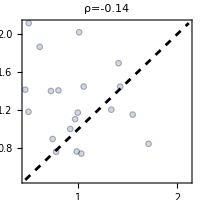
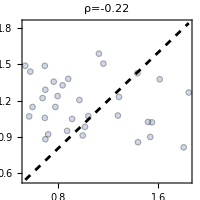
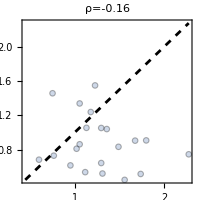

```mathematica
(* Using batch-corrected data *)
Table[
plotData=Cases[{assocDay0[{#,"Monocytes"}],assocSubjectCellFrequencyPost[{#,"Monocytes"}]/assocDay0[{#,"Monocytes"}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}]],{year,2020,2022}]
```

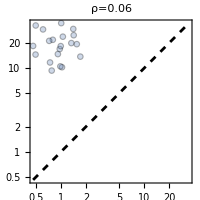
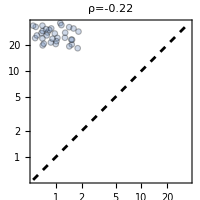
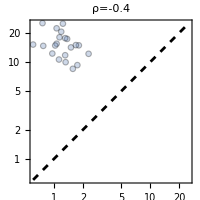

```mathematica
(* Using raw data *)
Table[
plotData=Cases[{assocDay0Raw[{#,"Monocytes"}],assocSubjectCellFrequencyPostRaw[{#,"Monocytes"}]/assocDay0Raw[{#,"Monocytes"}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

#### Batch corrected data: Searching for the best baseline feature

```mathematica
(* Using batch-corrected data *)
Quiet@SortBy[Mean/@Table[
plotData=Cases[{assocDay0[{#,feature}],assocSubjectCellFrequencyPost[{#,"Monocytes"}]/assocDay0[{#,"Monocytes"}]}&/@sera[year],{_?NumericQ..}];
{feature,SpearmanRho[First/@plotData,Last/@plotData]}
,{feature,Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures]},{year,2020,2022}],Last]
```

{{Proliferating B cells,-0.399098},{Activated B cells (ABCs),-0.346648},{CD56+CD3+T cells,-0.280277},{B cells (CD19+CD3-CD14-CD56-),-0.26654},{B cells (CD19+CD20+CD3-CD14-CD56-),-0.26236},{Naive B cells,-0.217191},{P48061,-0.204571},{Monocytes,-0.176961},{non-pDCs,-0.168761},{Classical_Monocytes,-0.163732},{cDC2,-0.161635},{Memory B cells,-0.159646},{IgG_FHA,-0.157956},{IgG_PRN,-0.155585},{CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells,-0.151706},{Conventional dendritic cells (cDCs),-0.149986},{CD3-CD19-CD56- cells,-0.133703},{TemCD8,-0.129359},{Intermediate_Monocytes,-0.114494},{Activated granulocytes,-0.112318},{Bcells,-0.10796},{TemraCD8,-0.107698},{CD8Tcells,-0.107543},{CD4+CD8+ T cells,-0.104973},{IgG1_FHA,-0.101794},{IgG2_PRN,-0.0977665},{P05231,-0.0972127},{YearsSinceBoost,-0.0800375},{P05112,-0.0731104},{Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-),-0.0492422},{cDC1,-0.0444574},{IgG2_FIM2/3,-0.0408537},{P80075,-0.0377011},{P35225,-0.0322058},{NaiveCD8,-0.0304016},{TemraCD4,-0.022568},{IgG1_FIM2/3,-0.0116696},{IgG1_PRN,-0.0112761},{IgG3_PT,-0.00784336},{Basophils,-0.00588697},{CD4Tcells,-0.00153554},{Q14116,-0.000790539},{Q8NEV9_Q14213,0.00323772},{Q969D9,0.00414095},{IgG2_TT,0.00493663},{IgG2_DT,0.0139654},{Non-Classical_Monocytes,0.0183131},{P13232,0.0192917},{IgG4_FHA,0.0204276},{IgG4_TT,0.0208276},{IgG4_OVA,0.0219868},{Age,0.0255408},{IgG1_DT,0.0259511},{TcmCD8,0.0268813},{NaiveCD4,0.0320825},{P40933,0.0338237},{IgG3_DT,0.0361818},{NK,0.0432072},{IgG3_PRN,0.0436024},{P04141,0.0450793},{P01584,0.0456729},{P49771,0.0469673},{P78380,0.0517925},{P15692,0.053455},{IgG4_DT,0.0620224},{CD56high NK cells,0.0627992},{IgG3_TT,0.0628575},{IgG4_PRN,0.0646009},{IgG2_PT,0.0653189},{IgG_PT,0.0670845},{TcmCD4,0.0673088},{IgG1_PT,0.0692106},{IgG4_FIM2/3,0.0699308},{Q96PD4,0.070117},{P39900,0.0723409},{IgG2_FHA,0.0809431},{Q16552,0.0814415},{CD4-CD8- T cells,0.0830183},{pDC,0.0877958},{IgG1_OVA,0.0911956},{NK cells (CD3-CD19-CD56+),0.0979234},{P80098,0.0982191},{CD3 Tcells,0.100818},{P01133,0.101177},{P09919,0.10151},{Q9P0M4,0.108143},{P22301,0.109351},{TemCD4,0.109817},{P09603,0.111279},{P01374,0.11179},{IgG2_OVA,0.119413},{Q07325,0.124103},{P50591,0.132247},{IgG3_FHA,0.135566},{P02778,0.135689},{IgG3_FIM2/3,0.14709},{P13500,0.16217},{CD3CD19neg,0.163903},{P14210,0.17763},{P03956,0.185792},{Q99731,0.190636},{IgG4_PT,0.192942},{O43508,0.200224},{P13236,0.200792},{P10145,0.203522},{P51671,0.211524},{IgG3_OVA,0.21611},{P13725,0.216266},{P10147,0.229359},{P01135,0.245821},{O14625,0.278602},{IgG1_TT,0.297067},{Q99616,0.328016},{O95760,Indeterminate},{P01375,Indeterminate},{P01579,Indeterminate},{P60568,Indeterminate},{Sex,SpearmanRho[{},{}]},{VacType,SpearmanRho[{},{}]}}

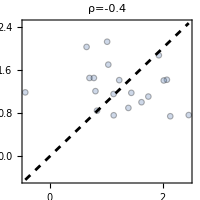
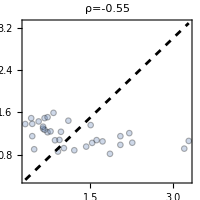
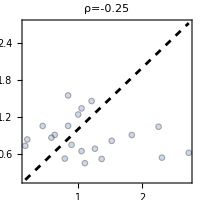

```mathematica
(* Using batch-corrected data *)
Table[
plotData=Cases[{assocDay0[{#,"Proliferating B cells"}],assocSubjectCellFrequencyPost[{#,"Monocytes"}]/assocDay0[{#,"Monocytes"}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}]],{year,2020,2022}]
```

#### Raw data: Searching for the best baseline feature

```mathematica
SortBy[
(* Using raw data *)
Mean/@Table[
plotData=Cases[{assocDay0Raw[{#,feature}],assocSubjectCellFrequencyPostRaw[{#,"Monocytes"}]/assocDay0Raw[{#,"Monocytes"}]}&/@sera[year],{_?NumericQ..}];
{feature,SpearmanRho[First/@plotData,Last/@plotData]}
,{feature,listCellFrequencyFeatures},{year,2020,2022}],Last]
```

{{Proliferating B cells,-0.365321},{Activated B cells (ABCs),-0.295678},{CD56+CD3+T cells,-0.262363},{B cells (CD19+CD3-CD14-CD56-),-0.26214},{B cells (CD19+CD20+CD3-CD14-CD56-),-0.254607},{Naive B cells,-0.211614},{Monocytes,-0.184974},{Classical_Monocytes,-0.173372},{cDC2,-0.170137},{non-pDCs,-0.16747},{Memory B cells,-0.159172},{CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells,-0.156837},{Conventional dendritic cells (cDCs),-0.154103},{CD3-CD19-CD56- cells,-0.152076},{CD4+CD8+ T cells,-0.134441},{Intermediate_Monocytes,-0.116023},{TemCD8,-0.0992076},{Activated granulocytes,-0.0933505},{CD8Tcells,-0.0850974},{Bcells,-0.0806384},{TemraCD8,-0.0758834},{TemraCD4,-0.042795},{NaiveCD8,-0.004706},{Basophils,-0.000668804},{CD4Tcells,0.00450415},{TcmCD8,0.00483628},{Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-),0.00996644},{NaiveCD4,0.0235483},{cDC1,0.0331788},{CD56high NK cells,0.0620113},{NK,0.0672266},{Non-Classical_Monocytes,0.0844819},{TcmCD4,0.09015},{TemCD4,0.0998137},{CD3 Tcells,0.108448},{CD4-CD8- T cells,0.121203},{pDC,0.159751},{NK cells (CD3-CD19-CD56+),0.160784},{CD3CD19neg,0.221061}}

#### Scratch: Raw one more time

Goal:

Let’s see whether adding any other feature leads to consistently better predictions against ever Ab feature. If it does, then we can consider adding it

After we add all such features (perhaps testing their combinations, make the final model to predict the 2022 results, and see whether this model actually does better than the base model (just using the baseline of the feature of interest)

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listCellFrequencyFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,"Proliferating B cells"];
predict=Predict[Cases[Table[assocDay0Raw[{#,feature}],{feature,features}]->assocSubjectCellFrequencyPostRaw[{#,featureOfInterest}]/assocDay0Raw[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0Raw[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectCellFrequencyPostRaw[{#,featureOfInterest}]/assocDay0Raw[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{}]
resBase[2021,2020]=analyze[2021,2020,{}]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

Predict::mlbddataev: The data being evaluated is not formatted correctly.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Predict::mlbddataev: The data being evaluated is not formatted correctly.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

Predict::mlbddataev: The data being evaluated is not formatted correctly.

General::stop: Further output of Predict::mlbddataev will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

{0.468849,0.432194,0.119719,0.2909,0.272608,-0.239326,-0.148113,-0.18103,-0.366219,0.208072,-0.461148,0.0464043,0.0497431,0.247693,-0.262027,0.0576093,0.151662,-0.297095,-0.202694,0.0166997,SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]]}

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

SpearmanRho::rctneqln: The arguments to SpearmanRho are not a pair of vectors or matrices of equal length.

General::stop: Further output of SpearmanRho::rctneqln will be suppressed during this calculation.

{0.386022,0.46701,0.311706,0.282822,-0.00823767,0.163713,0.0322024,-0.329427,-0.113055,0.0793057,-0.317191,0.23933,-0.328411,-0.169962,-0.276571,-0.0919152,-0.0827362,-0.206534,0.147486,0.0115461,SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]],SpearmanRho[First[{}],Last[{}]]}

⟨ρ⟩=  0.01

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2020,2021,newFeature]=analyze[2020,2021,newFeature];
resFeature[2021,2020,newFeature]=analyze[2021,2020,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2020,2021],resBase[2021,2020]],Join[resFeature[2020,2021,newFeature],resFeature[2021,2020,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,List/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]]}]
```

On:  {VacType}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Sex}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Age}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {YearsSinceBoost}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG_PT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG_PRN}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG_FHA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG1_PT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_PRN}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_FHA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG1_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG1_TT}

{ρ_base,ρ_new}  {0.59,0.6}

On:  {IgG1_DT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG1_OVA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_PT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_PRN}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG2_FHA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG2_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG2_TT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG2_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG3_PT}

{ρ_base,ρ_new}  {0.59,0.59}

On:  {IgG3_PRN}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG3_FHA}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_TT}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG3_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG3_OVA}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_PT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG4_PRN}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_FHA}

{ρ_base,ρ_new}  {0.59,0.58}

On:  {IgG4_FIM2/3}

{ρ_base,ρ_new}  {0.59,0.59}

On:  {IgG4_TT}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {IgG4_DT}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {IgG4_OVA}

{ρ_base,ρ_new}  {0.59,0.57}

On:  {P05231}

{ρ_base,ρ_new}  {0.59,0.54}

On:  {P51671}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {P22301}

{ρ_base,ρ_new}  {0.59,0.56}

On:  {P48061}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {P10145}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Classical_Monocytes}

{ρ_base,ρ_new}  {0.59,0.55}

On:  {Non-Classical_Monocytes}

{ρ_base,ρ_new}  {0.59,0.53}

On:  {Intermediate_Monocytes}

{ρ_base,ρ_new}  {0.59,0.53}

On:  {Bcells}

{ρ_base,ρ_new}  {0.59,0.58}

```mathematica
(* Cases where an additional feature seems to help *)
Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]],entry_/;entry[[-1]]>=entry[[-2]]]
```

{{YearsSinceBoost,0.589482,0.599505},{IgG1_FIM2/3,0.589482,0.600876},{IgG1_TT,0.589482,0.595514},{IgG3_PT,0.589482,0.591056}}

#### Testing, Searching through all features to add to Baseline

Goal:

Let’s see whether adding any other feature leads to consistently better predictions against ever Ab feature. If it does, then we can consider adding it

After we add all such features (perhaps testing their combinations, make the final model to predict the 2022 results, and see whether this model actually does better than the base model (just using the baseline of the feature of interest)

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listCellFrequencyFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,"Proliferating B cells"];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectCellFrequencyPost[{#,featureOfInterest}]/assocDay0[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectCellFrequencyPost[{#,featureOfInterest}]/assocDay0[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{}]
resBase[2021,2020]=analyze[2021,2020,{}]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.460688,0.456613,0.0380773,0.359472,-0.0497757,-0.257496,-0.202571,-0.31962,-0.356204,-0.0680436,-0.403755,0.0769305,-0.0623188,0.00712672,-0.32913,0.0516634,0.198889,-0.140963,-0.196957,0.0248921,0.229431,0.226694,-0.253144,0.203939,-0.143848,-0.207833,0.147472,0.340302,-0.456789,-0.388234,0.404978,-0.101987,-0.272396,0.0404048,0.033353,0.140287,-0.317321,0.0292549,0.172527}

Hacky move: Since not all of the cell features appear to be well predicted by anything, let’s look at the cases that can be well predicted. The idea here is to still get some sense of robustness, although I am now biasing things quite a bit by focusing on features that are already robustly predicted by Proliferating B cells...

```mathematica
Position[,val_/;val>0.3]
Position[,val_/;val>0.3]
```

{{1},{2},{4},{28},{31}}

{{1},{2},{21},{22},{24},{27},{31}}

```mathematica
Union@Flatten[{{{1},{2},{4},{28},{31}},{{1},{2},{21},{22},{24},{27},{31}}}]
```

{1,2,4,21,22,24,27,28,31}

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2020,2021]=analyze[2020,2021,{},listCellFrequencyFeatures[[{1,2,4,21,22,24,27,28,31}]]]
resBase[2021,2020]=analyze[2021,2020,{},listCellFrequencyFeatures[[{1,2,4,21,22,24,27,28,31}]]]
Echo[N@Mean@Cases[Join[resBase[2020,2021],resBase[2021,2020]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.460688,0.456613,0.359472,0.229431,0.226694,0.203939,0.147472,0.340302,0.404978}

{0.411909,0.397301,0.19,0.391345,0.383275,0.401962,0.339234,-0.106821,0.346451}

⟨ρ⟩=  0.31

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2020,2021,newFeature]=analyze[2020,2021,newFeature,listCellFrequencyFeatures[[{1,2,4,21,22,24,27,28,31}]]];
resFeature[2021,2020,newFeature]=analyze[2021,2020,newFeature,listCellFrequencyFeatures[[{1,2,4,21,22,24,27,28,31}]]];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2020,2021],resBase[2021,2020]],Join[resFeature[2020,2021,newFeature],resFeature[2021,2020,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,List/@{"Activated B cells (ABCs)","CD56+CD3+T cells","B cells (CD19+CD3-CD14-CD56-)","B cells (CD19+CD20+CD3-CD14-CD56-)","Naive B cells","P48061","Monocytes"}(*List/@Join[listDemographicFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listCellFrequencyFeatures[[;;5]]]*)}]
```

On:  {Activated B cells (ABCs)}

{ρ_base,ρ_new}  {0.31,0.3}

On:  {CD56+CD3+T cells}

{ρ_base,ρ_new}  {0.31,0.27}

On:  {B cells (CD19+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.31,0.3}

On:  {B cells (CD19+CD20+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.31,0.3}

On:  {Naive B cells}

{ρ_base,ρ_new}  {0.31,0.26}

On:  {P48061}

{ρ_base,ρ_new}  {0.31,0.31}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.31,0.31}

None of these moves seem to greatly benefit the results. I am going to throw Monocytes in simply because it is a reasonable feature to include. Hopefully it doesn’t hurt anything, and it should guarantee performance that isn’t too far off from the baseline model

#### Final Model: Using “Monocytes” and “Proliferating B cells”

```mathematica
Clear[combine]
combine[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listCellFrequencyFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectCellFrequencyPost[{#,featureOfInterest}]/assocDay0[{#,featureOfInterest}]&/@Join@@sera/@Flatten@List@yearTraining,HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData={
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],0}&/@sera[yearTesting];
{First@Transpose@plotData,Last@Transpose@plotData}
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
combine[2020,2023,{"Proliferating B cells"},listCellFrequencyFeatures[[{1}]]]
```

{{{1.02725,1.64309,1.56311,1.01925,1.08323,1.49913,1.64309,1.46714,1.05124,1.16321,1.47514,1.08323,1.01925,1.47514,1.02725,1.10723,1.06724,1.32317,1.45114,1.34717,1.02725,1.41115,Missing[],Missing[],1.07523,1.17921,1.47514,1.44314,1.11522,1.45114,Missing[],1.45114,Missing[],1.03524,Missing[],1.46714,1.01925,Missing[],1.05124,1.10723,1.01925,1.6271,1.33917,1.09923,1.34717,1.46714,1.46714,1.36316,1.43515,1.46714,1.34717,1.45114,1.09123,1.17121},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
res2020=combine[2020,2023,{"Proliferating B cells"},listCellFrequencyFeatures[[{1}]]];
res2021=combine[2021,2023,{"Proliferating B cells"},listCellFrequencyFeatures[[{1}]]];
res2022=combine[2022,2023,{"Proliferating B cells"},listCellFrequencyFeatures[[{1}]]];
(* Fill in missing values with random real. These should really be imputed, but apparently these people didn't have any post-vac measurement *)
res2020=res2020/.Missing[]->RandomReal[MinMax[DeleteMissing@res2020[[1,1]]]];
res2021=res2021/.Missing[]->RandomReal[MinMax[DeleteMissing@res2021[[1,1]]]];
res2022=res2022/.Missing[]->RandomReal[MinMax[DeleteMissing@res2022[[1,1]]]];
```

The 2021 data clearly has no impact, since it predicted the same value everywhere. Including it anyways, since it won’t affect anything

```mathematica
predictTask[2.2]=Mean/@Transpose@{res2020[[1,1]],res2021[[1,1]],res2022[[1,1]]}
```

{0.979885,1.31817,1.28689,0.989711,0.940707,1.22924,1.31817,1.18394,0.929415,1.04705,1.24935,0.940707,0.92223,1.2522,0.922842,1.01983,0.9368,1.10465,1.23896,1.13125,1.00247,1.22055,1.12459,1.12459,1.01202,1.05523,1.2522,1.23629,1.04332,1.17307,1.12459,1.25464,1.12459,1.00075,1.12459,1.24982,0.918123,1.12459,0.932894,1.02235,0.989253,1.31283,1.11916,1.02874,1.07706,1.26043,1.25381,1.16253,1.23488,1.26248,1.07563,1.17307,1.01274,1.05542}

```mathematica
predictTask[2.2]={0.9798850416055696,1.31816632948187,1.2868890090553944,0.9897105917501797,0.9407065817057015,1.2292374202673566,1.31816632948187,1.1839370753095928,0.9294147172109607,1.04705096373713,1.2493486238226927,0.9407065817057015,0.9222300249803075,1.2522000967005902,0.9228424425486749,1.0198345192005585,0.9368003107438274,1.1046482470622039,1.238956952483899,1.1312462718866563,1.0024744890580537,1.220551837919143,1.1245945119581824,1.1245945119581824,1.0120219772768102,1.05523444401585,1.2522000967005902,1.2362909487834874,1.0433241598089897,1.1730721592057332,1.1245945119581824,1.2546400533123336,1.1245945119581824,1.000745544906797,1.1245945119581824,1.2498218685877585,0.9181228527162194,1.1245945119581824,0.9328940397819533,1.0223459179729402,0.9892527791098423,1.312834322081047,1.1191625227898137,1.0287444440644937,1.077055145707659,1.2604298733534942,1.2538113023170245,1.1625293107761336,1.234880644469267,1.262483459485538,1.0756294092687104,1.1730721592057332,1.0127367012552715,1.0554199131933357};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[2.2]]
```

{46,1,4,44,47,16,2,18,51,35,12,48,53,9,52,39,49,30,13,22,42,17,23,24,41,34,10,14,36,19,25,7,26,43,27,11,54,28,50,38,45,3,29,37,31,6,8,21,15,5,32,20,40,33}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,8]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 |  | 46 |  |  | 
120 | 27 | Female | wP | 4 | 40 |  | 1 |  |  | 
121 | 22 | Female | aP | 27 | 20 |  | 4 |  |  | 
122 | 23 | Female | aP | 2 | 44 |  | 44 |  |  | 
123 | 26 | Female | wP | 1 | 48 |  | 47 |  |  | 
124 | 22 | Male | aP | 28 | 11 |  | 16 |  |  | 
125 | 29 | Male | wP | 26 | 29 |  | 2 |  |  | 
126 | 29 | Male | wP | 23 | 28 |  | 18 |  |  | 
127 | 26 | Female | aP | 29 | 13 |  | 51 |  |  | 
128 | 28 | Female | wP | 20 | 32 |  | 35 |  |  | 
129 | 31 | Male | wP | 30 | 17 |  | 12 |  |  | 
130 | 26 | Male | wP | 21 | 35 |  | 48 |  |  | 
131 | 24 | Female | aP | 31 | 12 |  | 53 |  |  | 
132 | 27 | Male | wP | 5 | 41 |  | 9 |  |  | 
133 | 25 | Female | aP | 22 | 34 |  | 52 |  |  | 
134 | 32 | Male | wP | 48 | 6 |  | 39 |  |  | 
135 | 27 | Male | wP | 32 | 9 |  | 49 |  |  | 
136 | 27 | Female | wP | 33 | 18 |  | 30 |  |  | 
137 | 24 | Female | aP | 34 | 19 |  | 13 |  |  | 
138 | 22 | Male | aP | 6 | 38 |  | 22 |  |  | 
139 | 29 | Female | wP | 35 | 15 |  | 42 |  |  | 
140 | 21 | Female | aP | 36 | 21 |  | 17 |  |  | 
141 | 26 | Female | wP | 24 | 27 |  | 23 |  |  | 
142 | 31 | Female | aP | 50 | 5 |  | 24 |  |  | 
143 | 19 | Female | aP | 37 | 33 |  | 41 |  |  | 
144 | 23 | Female | aP | 12 | 53 |  | 34 |  |  | 
145 | 20 | Male | aP | 52 | 3 |  | 10 |  |  | 
146 | 31 | Male | wP | 7 | 54 |  | 14 |  |  | 
147 | 23 | Female | aP | 8 | 50 |  | 36 |  |  | 
148 | 35 | Male | wP | 39 | 25 |  | 19 |  |  | 
149 | 32 | Female | wP | 9 | 51 |  | 25 |  |  | 
150 | 32 | Male | wP | 13 | 45 |  | 7 |  |  | 
151 | 31 | Female | wP | 51 | 4 |  | 26 |  |  | 
152 | 28 | Female | wP | 17 | 37 |  | 43 |  |  | 
153 | 25 | Female | aP | 40 | 23 |  | 27 |  |  | 
154 | 26 | Female | aP | 49 | 7 |  | 11 |  |  | 
155 | 26 | Female | aP | 38 | 26 |  | 54 |  |  | 
156 | 22 | Female | aP | 14 | 46 |  | 28 |  |  | 
157 | 26 | Female | aP | 18 | 39 |  | 50 |  |  | 
158 | 23 | Male | aP | 15 | 47 |  | 38 |  |  | 
159 | 29 | Female | wP | 41 | 24 |  | 45 |  |  | 
160 | 27 | Male | aP | 10 | 52 |  | 3 |  |  | 
161 | 30 | Female | aP | 19 | 36 |  | 29 |  |  | 
162 | 24 | Female | aP | 42 | 30 |  | 37 |  |  | 
163 | 30 | Female | wP | 53 | 1 |  | 31 |  |  | 
164 | 32 | Male | wP | 16 | 43 |  | 6 |  |  | 
165 | 30 | Female | wP | 43 | 31 |  | 8 |  |  | 
166 | 22 | Female | aP | 44 | 14 |  | 21 |  |  | 
167 | 26 | Male | aP | 54 | 2 |  | 15 |  |  | 
168 | 32 | Male | wP | 11 | 49 |  | 5 |  |  | 
169 | 20 | Male | aP | 45 | 8 |  | 32 |  |  | 
170 | 31 | Male | wP | 46 | 16 |  | 20 |  |  | 
171 | 20 | Female | wP | 47 | 10 |  | 40 |  |  | 
172 | 36 | Male | wP | 25 | 22 |  | 33 |  |  |

## Task 3

Goal: Predict tpm of ENSG00000277632.1 (which stands for CCL3)

### Task 3.1

For this task, overwrite assocDay0 to include gene expression data

```mathematica
(* Combined association with everything we may need (except gene expression) *)
assocDay0=Association[Join@@Normal/@{assocSubjectDemographics,assocSubjectAbDay0,assocSubjectCellFrequencyDay0,assocSubjectCytokineDay0,assocSubjectGeneExpressionDay0,assocSubjectTCellActivationDay0,assocSubjectTCellPolarizationDay0}];
```

#### Using Baseline alone

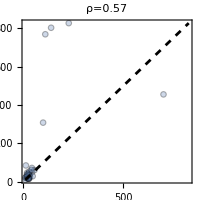
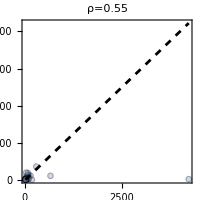
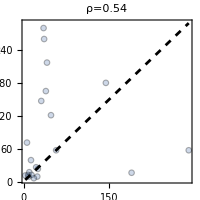

```mathematica
Table[
plotData=DeleteMissing[Transpose@{assocDay0/@({#,gene}&/@sera[year]),assocSubjectGeneExpressionPost/@({#,gene}&/@sera[year])},1,All];
plot[plotData,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ImageSize->200]
,{year,2020,2022}]
```

Conclusion: Using baseline is an excellent (and consistent!) good predictor of a feature’s post-vac value

#### Final Model: Using Baseline

```mathematica
SeedRandom[12345];
res2023=assocDay0/@({#,gene}&/@sera[2023]);
(* Fill in missing values with random real. These should really be imputed, but apparently these people didn't have any post-vac measurement *)
res2023=res2023/._Missing->RandomReal[MinMax[DeleteMissing@res2023]];
```

```mathematica
predictTask[3.1]=res2023
```

{14,55.8633,47,60,29,74,294,30,17,5,8,22,36,6,10,9,66,17,42,25,73,15,8,24,9,15,12,18,9,3,108,35,14,29,83,202,6,439,278,62,191,30,31,15,135,102,6,256,383,224,75,45,43,103}

```mathematica
predictTask[3.1]={14,55.86334277175314,47,60,29,74,294,30,17,5,8,22,36,6,10,9,66,17,42,25,73,15,8,24,9,15,12,18,9,3,108,35,14,29,83,202,6,439,278,62,191,30,31,15,135,102,6,256,383,224,75,45,43,103};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[3.1]]
```

{41,20,21,19,30,15,3,28,36,53,48,34,25,50,44,45,17,37,24,32,16,38,49,33,46,39,43,35,47,54,10,26,42,31,13,7,51,1,4,18,8,29,27,40,9,12,52,5,2,6,14,22,23,11}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,9]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 | 23 | 46 | 41 |  | 
120 | 27 | Female | wP | 4 | 40 | 52 | 1 | 20 |  | 
121 | 22 | Female | aP | 27 | 20 | 54 | 4 | 21 |  | 
122 | 23 | Female | aP | 2 | 44 | 42 | 44 | 19 |  | 
123 | 26 | Female | wP | 1 | 48 | 18 | 47 | 30 |  | 
124 | 22 | Male | aP | 28 | 11 | 51 | 16 | 15 |  | 
125 | 29 | Male | wP | 26 | 29 | 53 | 2 | 3 |  | 
126 | 29 | Male | wP | 23 | 28 | 14 | 18 | 28 |  | 
127 | 26 | Female | aP | 29 | 13 | 15 | 51 | 36 |  | 
128 | 28 | Female | wP | 20 | 32 | 47 | 35 | 53 |  | 
129 | 31 | Male | wP | 30 | 17 | 41 | 12 | 48 |  | 
130 | 26 | Male | wP | 21 | 35 | 19 | 48 | 34 |  | 
131 | 24 | Female | aP | 31 | 12 | 16 | 53 | 25 |  | 
132 | 27 | Male | wP | 5 | 41 | 43 | 9 | 50 |  | 
133 | 25 | Female | aP | 22 | 34 | 17 | 52 | 44 |  | 
134 | 32 | Male | wP | 48 | 6 | 45 | 39 | 45 |  | 
135 | 27 | Male | wP | 32 | 9 | 20 | 49 | 17 |  | 
136 | 27 | Female | wP | 33 | 18 | 50 | 30 | 37 |  | 
137 | 24 | Female | aP | 34 | 19 | 46 | 13 | 24 |  | 
138 | 22 | Male | aP | 6 | 38 | 21 | 22 | 32 |  | 
139 | 29 | Female | wP | 35 | 15 | 22 | 42 | 16 |  | 
140 | 21 | Female | aP | 36 | 21 | 30 | 17 | 38 |  | 
141 | 26 | Female | wP | 24 | 27 | 24 | 23 | 49 |  | 
142 | 31 | Female | aP | 50 | 5 | 25 | 24 | 33 |  | 
143 | 19 | Female | aP | 37 | 33 | 40 | 41 | 46 |  | 
144 | 23 | Female | aP | 12 | 53 | 35 | 34 | 39 |  | 
145 | 20 | Male | aP | 52 | 3 | 32 | 10 | 43 |  | 
146 | 31 | Male | wP | 7 | 54 | 31 | 14 | 35 |  | 
147 | 23 | Female | aP | 8 | 50 | 1 | 36 | 47 |  | 
148 | 35 | Male | wP | 39 | 25 | 4 | 19 | 54 |  | 
149 | 32 | Female | wP | 9 | 51 | 26 | 25 | 10 |  | 
150 | 32 | Male | wP | 13 | 45 | 38 | 7 | 26 |  | 
151 | 31 | Female | wP | 51 | 4 | 27 | 26 | 42 |  | 
152 | 28 | Female | wP | 17 | 37 | 33 | 43 | 31 |  | 
153 | 25 | Female | aP | 40 | 23 | 28 | 27 | 13 |  | 
154 | 26 | Female | aP | 49 | 7 | 10 | 11 | 7 |  | 
155 | 26 | Female | aP | 38 | 26 | 5 | 54 | 51 |  | 
156 | 22 | Female | aP | 14 | 46 | 29 | 28 | 1 |  | 
157 | 26 | Female | aP | 18 | 39 | 6 | 50 | 4 |  | 
158 | 23 | Male | aP | 15 | 47 | 7 | 38 | 18 |  | 
159 | 29 | Female | wP | 41 | 24 | 34 | 45 | 8 |  | 
160 | 27 | Male | aP | 10 | 52 | 44 | 3 | 29 |  | 
161 | 30 | Female | aP | 19 | 36 | 48 | 29 | 27 |  | 
162 | 24 | Female | aP | 42 | 30 | 36 | 37 | 40 |  | 
163 | 30 | Female | wP | 53 | 1 | 8 | 31 | 9 |  | 
164 | 32 | Male | wP | 16 | 43 | 12 | 6 | 12 |  | 
165 | 30 | Female | wP | 43 | 31 | 39 | 8 | 52 |  | 
166 | 22 | Female | aP | 44 | 14 | 37 | 21 | 5 |  | 
167 | 26 | Male | aP | 54 | 2 | 13 | 15 | 2 |  | 
168 | 32 | Male | wP | 11 | 49 | 2 | 5 | 6 |  | 
169 | 20 | Male | aP | 45 | 8 | 9 | 32 | 14 |  | 
170 | 31 | Male | wP | 46 | 16 | 3 | 20 | 22 |  | 
171 | 20 | Female | wP | 47 | 10 | 11 | 40 | 23 |  | 
172 | 36 | Male | wP | 25 | 22 | 49 | 33 | 11 |  |

### Task 3.2

For this task, overwrite assocDay0 to include gene expression data

```mathematica
(* Combined association with everything we may need (except gene expression) *)
assocDay0=Association[Join@@Normal/@{assocSubjectDemographics,assocSubjectAbDay0,assocSubjectCellFrequencyDay0,assocSubjectCytokineDay0,assocSubjectGeneExpressionDay0,assocSubjectTCellActivationDay0,assocSubjectTCellPolarizationDay0}];
```

```mathematica
assocDay0Raw=Association[Join@@Normal/@{assocSubjectDemographics,assocSubjectAbDay0Raw,assocSubjectCellFrequencyDay0,assocSubjectCytokineDay0,assocSubjectGeneExpressionDay0,assocSubjectTCellActivationDay0,assocSubjectTCellPolarizationDay0}];
```

#### Using Baseline alone

It appears to be a mistake to use batch corrected data. Using raw data instead

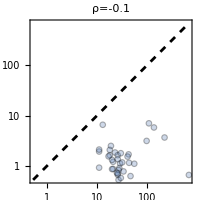
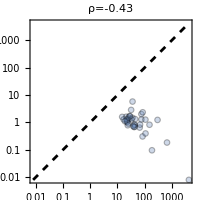
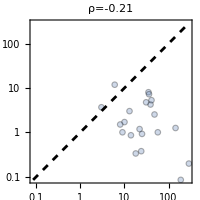

```mathematica
(* Using batch-corrected data *)
Table[
plotData=Cases[{assocDay0[{#,gene}],assocSubjectGeneExpressionPost[{#,gene}]/assocDay0[{#,gene}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

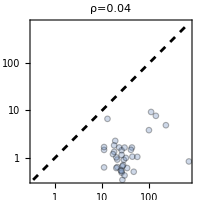
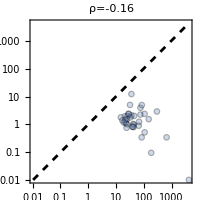
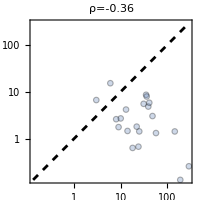

```mathematica
(* Using raw data *)
Table[
plotData=Cases[{assocDay0Raw[{#,gene}],assocSubjectGeneExpressionPostRaw[{#,gene}]/assocDay0Raw[{#,gene}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

#### Raw data: Searching for the best baseline feature

```mathematica
Quiet@SortBy[
Cases[
Mean/@Table[
plotData=Cases[{assocDay0Raw[{#,feature}],assocSubjectGeneExpressionPostRaw[{#,gene}]/assocDay0Raw[{#,gene}]}&/@sera[year],{_?NumericQ..}];
{feature,SpearmanRho[First/@plotData,Last/@plotData]}
,{feature,Join[listDemographicFeatures,listAbFeatures,listCellFrequencyFeatures,listGeneExpressionFeatures,listCytokineFeatures]},{year,2020,2022}]
,{_,_?NumericQ}],Last]
```

No features are consistently good. On average, these are two of the best, yet they do poorly in 2020. Going with the first one as an inverse correlation

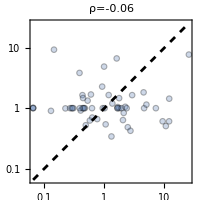
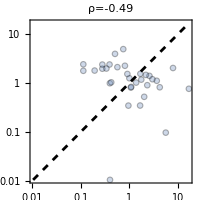
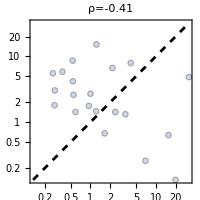

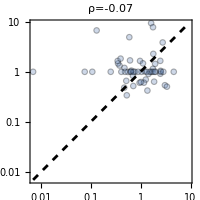
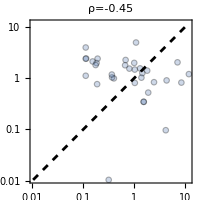
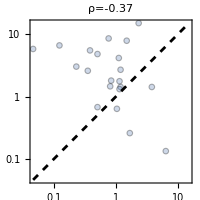

```mathematica
(* Using raw data *)
Table[
plotData=Cases[{assocDay0Raw[{#,"IgG2_FHA"}],assocSubjectGeneExpressionPostRaw[{#,gene}]/assocDay0Raw[{#,gene}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
(* Using raw data *)
Table[
plotData=Cases[{assocDay0Raw[{#,"IgG2_DT"}],assocSubjectGeneExpressionPostRaw[{#,gene}]/assocDay0Raw[{#,gene}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

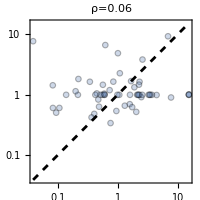
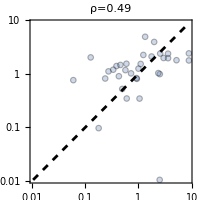
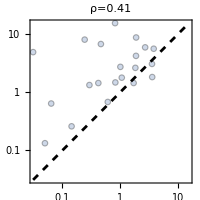

```mathematica
(* Using raw data *)
Table[
plotData=Cases[{1/assocDay0Raw[{#,"IgG2_FHA"}],assocSubjectGeneExpressionPostRaw[{#,gene}]/assocDay0Raw[{#,gene}]}&/@sera[year],{_?NumericQ..}];
plot[plotData,ImageSize->200,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ScalingFunctions->{"Log","Log"}],{year,2020,2022}]
```

#### Final Model: Using 1/baseline IgG2_FHA

```mathematica
res2023=1/assocDay0Raw[{#,"IgG2_FHA"}]&/@sera[2023]
```

{1.5625,0.894135,1.51431,0.590223,1.47944,0.498891,1.85464,0.825987,0.979847,1.06073,0.401742,0.397833,0.230819,1.13003,0.0989658,1.75,1.25628,0.365353,1.55623,0.38066,0.484123,0.425095,1.21554,1.75,2.59222,0.55049,1.08898,3.78737,0.971382,0.119048,1.51431,20.9186,0.151515,0.10661,0.280218,20.9186,0.178571,0.0305064,0.0293083,0.537634,1.5625,6.25,6.25,0.0316456,2.08333,6.25,2.77778,0.271739,2.77778,1.78571,4.16667,0.78125,0.118203,1.5625}

```mathematica
predictTask[2.2]=res2023
```

{1.5625,0.894135,1.51431,0.590223,1.47944,0.498891,1.85464,0.825987,0.979847,1.06073,0.401742,0.397833,0.230819,1.13003,0.0989658,1.75,1.25628,0.365353,1.55623,0.38066,0.484123,0.425095,1.21554,1.75,2.59222,0.55049,1.08898,3.78737,0.971382,0.119048,1.51431,20.9186,0.151515,0.10661,0.280218,20.9186,0.178571,0.0305064,0.0293083,0.537634,1.5625,6.25,6.25,0.0316456,2.08333,6.25,2.77778,0.271739,2.77778,1.78571,4.16667,0.78125,0.118203,1.5625}

```mathematica
predictTask[3.2]={1.5625,0.8941351888667989,1.5143097643097643,0.5902230971128618,1.4794407894736852,0.4988907376594568,1.8546391752577314,0.8259871441689648,0.9798474945533729,1.0607311320754718,0.4017418490397496,0.3978328173374615,0.23081857839363595,1.1300251256281408,0.09896578281439064,1.7500000000000016,1.2562849162011167,0.3653533712428914,1.5562283737024218,0.38066017774016014,0.4841227125941861,0.42509451795841185,1.2155405405405402,1.7500000000000016,2.5922190201729114,0.5504895960832311,1.0889830508474574,3.7873684210526317,0.9713822894168455,0.11904761904761904,1.5143097643097643,20.918604651162806,0.15151515151515152,0.10660980810234541,0.28021806853582565,20.918604651162806,0.17857142857142858,0.03050640634533252,0.02930832356389215,0.5376344086021505,1.5625,6.25,6.25,0.03164556962025316,2.0833333333333335,6.25,2.7777777777777777,0.2717391304347826,2.7777777777777777,1.7857142857142856,4.166666666666667,0.78125,0.11820330969267138,1.5625};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[3.2]]
```

{16,30,20,33,22,36,12,31,28,27,39,40,45,25,51,14,23,42,19,41,37,38,24,15,10,34,26,7,29,48,21,1,47,50,43,2,46,53,54,35,17,3,4,52,11,5,8,44,9,13,6,32,49,18}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,10]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 | 23 | 46 | 41 | 16 | 
120 | 27 | Female | wP | 4 | 40 | 52 | 1 | 20 | 30 | 
121 | 22 | Female | aP | 27 | 20 | 54 | 4 | 21 | 20 | 
122 | 23 | Female | aP | 2 | 44 | 42 | 44 | 19 | 33 | 
123 | 26 | Female | wP | 1 | 48 | 18 | 47 | 30 | 22 | 
124 | 22 | Male | aP | 28 | 11 | 51 | 16 | 15 | 36 | 
125 | 29 | Male | wP | 26 | 29 | 53 | 2 | 3 | 12 | 
126 | 29 | Male | wP | 23 | 28 | 14 | 18 | 28 | 31 | 
127 | 26 | Female | aP | 29 | 13 | 15 | 51 | 36 | 28 | 
128 | 28 | Female | wP | 20 | 32 | 47 | 35 | 53 | 27 | 
129 | 31 | Male | wP | 30 | 17 | 41 | 12 | 48 | 39 | 
130 | 26 | Male | wP | 21 | 35 | 19 | 48 | 34 | 40 | 
131 | 24 | Female | aP | 31 | 12 | 16 | 53 | 25 | 45 | 
132 | 27 | Male | wP | 5 | 41 | 43 | 9 | 50 | 25 | 
133 | 25 | Female | aP | 22 | 34 | 17 | 52 | 44 | 51 | 
134 | 32 | Male | wP | 48 | 6 | 45 | 39 | 45 | 14 | 
135 | 27 | Male | wP | 32 | 9 | 20 | 49 | 17 | 23 | 
136 | 27 | Female | wP | 33 | 18 | 50 | 30 | 37 | 42 | 
137 | 24 | Female | aP | 34 | 19 | 46 | 13 | 24 | 19 | 
138 | 22 | Male | aP | 6 | 38 | 21 | 22 | 32 | 41 | 
139 | 29 | Female | wP | 35 | 15 | 22 | 42 | 16 | 37 | 
140 | 21 | Female | aP | 36 | 21 | 30 | 17 | 38 | 38 | 
141 | 26 | Female | wP | 24 | 27 | 24 | 23 | 49 | 24 | 
142 | 31 | Female | aP | 50 | 5 | 25 | 24 | 33 | 15 | 
143 | 19 | Female | aP | 37 | 33 | 40 | 41 | 46 | 10 | 
144 | 23 | Female | aP | 12 | 53 | 35 | 34 | 39 | 34 | 
145 | 20 | Male | aP | 52 | 3 | 32 | 10 | 43 | 26 | 
146 | 31 | Male | wP | 7 | 54 | 31 | 14 | 35 | 7 | 
147 | 23 | Female | aP | 8 | 50 | 1 | 36 | 47 | 29 | 
148 | 35 | Male | wP | 39 | 25 | 4 | 19 | 54 | 48 | 
149 | 32 | Female | wP | 9 | 51 | 26 | 25 | 10 | 21 | 
150 | 32 | Male | wP | 13 | 45 | 38 | 7 | 26 | 1 | 
151 | 31 | Female | wP | 51 | 4 | 27 | 26 | 42 | 47 | 
152 | 28 | Female | wP | 17 | 37 | 33 | 43 | 31 | 50 | 
153 | 25 | Female | aP | 40 | 23 | 28 | 27 | 13 | 43 | 
154 | 26 | Female | aP | 49 | 7 | 10 | 11 | 7 | 2 | 
155 | 26 | Female | aP | 38 | 26 | 5 | 54 | 51 | 46 | 
156 | 22 | Female | aP | 14 | 46 | 29 | 28 | 1 | 53 | 
157 | 26 | Female | aP | 18 | 39 | 6 | 50 | 4 | 54 | 
158 | 23 | Male | aP | 15 | 47 | 7 | 38 | 18 | 35 | 
159 | 29 | Female | wP | 41 | 24 | 34 | 45 | 8 | 17 | 
160 | 27 | Male | aP | 10 | 52 | 44 | 3 | 29 | 3 | 
161 | 30 | Female | aP | 19 | 36 | 48 | 29 | 27 | 4 | 
162 | 24 | Female | aP | 42 | 30 | 36 | 37 | 40 | 52 | 
163 | 30 | Female | wP | 53 | 1 | 8 | 31 | 9 | 11 | 
164 | 32 | Male | wP | 16 | 43 | 12 | 6 | 12 | 5 | 
165 | 30 | Female | wP | 43 | 31 | 39 | 8 | 52 | 8 | 
166 | 22 | Female | aP | 44 | 14 | 37 | 21 | 5 | 44 | 
167 | 26 | Male | aP | 54 | 2 | 13 | 15 | 2 | 9 | 
168 | 32 | Male | wP | 11 | 49 | 2 | 5 | 6 | 13 | 
169 | 20 | Male | aP | 45 | 8 | 9 | 32 | 14 | 6 | 
170 | 31 | Male | wP | 46 | 16 | 3 | 20 | 22 | 32 | 
171 | 20 | Female | wP | 47 | 10 | 11 | 40 | 23 | 49 | 
172 | 36 | Male | wP | 25 | 22 | 49 | 33 | 11 | 18 |

## Task 4

### Task 4.1

Goal: Predict the Th1/Th2 (IFN-γ/IL-5) polarization ratio on Day 30
Note: Data only available from 2021-2023 (not 2020)

#### Using Baseline alone

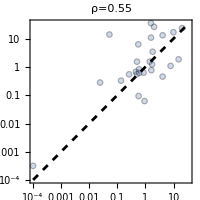
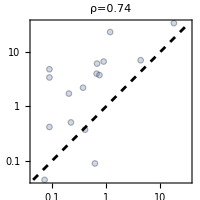

```mathematica
Table[
plotData=DeleteMissing[Transpose@{assocDay0[{#,"PT_P01579"}]/assocDay0[{#,"PT_P05113"}]&/@sera[year],assocSubjectTCellPolarizationPost[{#,"PT_P01579"}]/assocSubjectTCellPolarizationPost[{#,"PT_P05113"}]&/@sera[year]},1,All];
plot[plotData,PlotLabel->Row[{"ρ=",Round[SpearmanRho[First/@plotData,Last/@plotData],0.01]}],ImageSize->200,loglog]
,{year,2021,2022}]
```

Conclusion: Using baseline is an excellent (and consistent!) good predictor of a feature’s post-vac value

#### Testing, Searching through all features to add to Baseline

```mathematica
Clear[analyze]
analyze[yearTraining_,yearTesting_,extraFeatures_List,featuresToTest_:listTCellPolarizationFeatures]:=Block[{input,plotData,predict,features},
Table[
features=Prepend[extraFeatures,featureOfInterest];
predict=Predict[Cases[Table[assocDay0[{#,feature}],{feature,features}]->assocSubjectTCellPolarizationPost[{#,featureOfInterest}]&/@sera[yearTraining],HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData=Cases[{
input=Table[assocDay0[{#,feature}],{feature,features}];
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],assocSubjectTCellPolarizationPost[{#,featureOfInterest}]}&/@sera[yearTesting],{_?NumericQ..}];
If[Or@@Equal@@@MinMax/@Transpose@plotData,
(* Zero variance, statistic cannot be computed *)
Indeterminate,
SpearmanRho[First@Transpose@plotData,Last@Transpose@plotData]
]
,{featureOfInterest,featuresToTest}]
]
```

```mathematica
(* Just using the pre-vac titer for the feature-of-interest *)
resBase[2021,2022]=analyze[2021,2022,{}]
resBase[2022,2021]=analyze[2022,2021,{}]
Echo[N@Mean@Cases[Join[resBase[2021,2022],resBase[2022,2021]],_?NumericQ],"⟨ρ⟩=",Round[#,0.01]&];
```

{0.615393,0.740385,0.670765,0.566825,0.119963,0.257464}

{0.707746,0.323992,0.590861,0.346451,0.155945,0.313518}

⟨ρ⟩=  0.45

```mathematica
(* Trying all features with a hope of success *)
Do[
Echo[newFeature,"On:"];
resFeature[2021,2022,newFeature]=analyze[2021,2022,newFeature];
resFeature[2022,2021,newFeature]=analyze[2022,2021,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2021,2022],resBase[2022,2021]],Join[resFeature[2021,2022,newFeature],resFeature[2022,2021,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,(List/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listTCellPolarizationFeatures])}]
```

On:  {VacType}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {Sex}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {Age}

{ρ_base,ρ_new}  {0.45,0.39}

On:  {YearsSinceBoost}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {Monocytes}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {Classical_Monocytes}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {Non-Classical_Monocytes}

{ρ_base,ρ_new}  {0.45,0.4}

On:  {Intermediate_Monocytes}

{ρ_base,ρ_new}  {0.45,0.5}

On:  {Bcells}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {CD3CD19neg}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {CD3 Tcells}

{ρ_base,ρ_new}  {0.45,0.42}

On:  {CD4Tcells}

{ρ_base,ρ_new}  {0.45,0.38}

On:  {CD8Tcells}

{ρ_base,ρ_new}  {0.45,0.43}

On:  {TemraCD4}

{ρ_base,ρ_new}  {0.45,0.4}

On:  {NaiveCD4}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {TemCD4}

{ρ_base,ρ_new}  {0.45,0.35}

On:  {TcmCD4}

{ρ_base,ρ_new}  {0.45,0.39}

On:  {TemraCD8}

{ρ_base,ρ_new}  {0.45,0.38}

On:  {NaiveCD8}

{ρ_base,ρ_new}  {0.45,0.38}

On:  {TemCD8}

{ρ_base,ρ_new}  {0.45,0.42}

On:  {TcmCD8}

{ρ_base,ρ_new}  {0.45,0.51}

On:  {NK}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {Basophils}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {pDC}

{ρ_base,ρ_new}  {0.45,0.5}

On:  {B cells (CD19+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {B cells (CD19+CD20+CD3-CD14-CD56-)}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {Memory B cells}

{ρ_base,ρ_new}  {0.45,0.48}

On:  {Naive B cells}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {Proliferating B cells}

{ρ_base,ρ_new}  {0.45,0.4}

On:  {Activated B cells (ABCs)}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {CD56+CD3+T cells}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {CD4+CD8+ T cells}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {CD4-CD8- T cells}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {NK cells (CD3-CD19-CD56+)}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {CD3-CD19-CD56- cells}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {non-pDCs}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells}

{ρ_base,ρ_new}  {0.45,0.55}

On:  {Conventional dendritic cells (cDCs)}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {cDC1}

{ρ_base,ρ_new}  {0.45,0.37}

On:  {cDC2}

{ρ_base,ρ_new}  {0.45,0.43}

On:  {Activated granulocytes}

{ρ_base,ρ_new}  {0.45,0.5}

On:  {Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-)}

{ρ_base,ρ_new}  {0.45,0.42}

On:  {CD56high NK cells}

{ρ_base,ρ_new}  {0.45,0.5}

On:  {IgG_PT}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {IgG_PRN}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG_FHA}

{ρ_base,ρ_new}  {0.45,0.35}

On:  {IgG1_PT}

{ρ_base,ρ_new}  {0.45,0.43}

On:  {IgG1_PRN}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {IgG1_FHA}

{ρ_base,ρ_new}  {0.45,0.34}

On:  {IgG1_FIM2/3}

{ρ_base,ρ_new}  {0.45,0.36}

On:  {IgG1_TT}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {IgG1_DT}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG1_OVA}

{ρ_base,ρ_new}  {0.45,0.42}

On:  {IgG2_PT}

{ρ_base,ρ_new}  {0.45,0.48}

On:  {IgG2_PRN}

{ρ_base,ρ_new}  {0.45,0.38}

On:  {IgG2_FHA}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {IgG2_FIM2/3}

{ρ_base,ρ_new}  {0.45,0.43}

On:  {IgG2_TT}

{ρ_base,ρ_new}  {0.45,0.44}

On:  {IgG2_DT}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.45,0.54}

On:  {IgG3_PT}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG3_PRN}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG3_FHA}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG3_FIM2/3}

{ρ_base,ρ_new}  {0.45,0.48}

On:  {IgG3_TT}

{ρ_base,ρ_new}  {0.45,0.39}

On:  {IgG3_DT}

{ρ_base,ρ_new}  {0.45,0.47}

On:  {IgG3_OVA}

{ρ_base,ρ_new}  {0.45,0.48}

On:  {IgG4_PT}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {IgG4_PRN}

{ρ_base,ρ_new}  {0.45,0.37}

On:  {IgG4_FHA}

{ρ_base,ρ_new}  {0.45,0.5}

On:  {IgG4_FIM2/3}

{ρ_base,ρ_new}  {0.45,0.49}

On:  {IgG4_TT}

{ρ_base,ρ_new}  {0.45,0.48}

On:  {IgG4_DT}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {IgG4_OVA}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {P05231}

{ρ_base,ρ_new}  {0.45,0.4}

On:  {P51671}

{ρ_base,ρ_new}  {0.45,0.35}

On:  {P22301}

{ρ_base,ρ_new}  {0.45,0.4}

On:  {P48061}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {P10145}

{ρ_base,ρ_new}  {0.45,0.38}

On:  {PHA_P01579}

{ρ_base,ρ_new}  {0.45,0.43}

On:  {PHA_Q16552}

{ρ_base,ρ_new}  {0.45,0.46}

On:  {PHA_P05113}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {PT_P01579}

{ρ_base,ρ_new}  {0.45,0.45}

On:  {PT_Q16552}

{ρ_base,ρ_new}  {0.45,0.41}

On:  {PT_P05113}

{ρ_base,ρ_new}  {0.45,0.44}

```mathematica
(* Cases where an additional feature seems to help *)
Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listTCellPolarizationFeatures],entry_/;entry[[-1]]>=entry[[-2]]]
```

```mathematica
(* Cases where an additional feature seems to help *)
ReverseSortBy[Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listTCellPolarizationFeatures],entry_/;entry[[-1]]>=entry[[-2]]],Last][[;;10]]
```

{{CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells,0.450776,0.548703},{IgG2_OVA,0.450776,0.537538},{TcmCD8,0.450776,0.511026},{Activated granulocytes,0.450776,0.504521},{CD56high NK cells,0.450776,0.50211},{Intermediate_Monocytes,0.450776,0.500718},{IgG4_FHA,0.450776,0.500459},{pDC,0.450776,0.500226},{VacType,0.450776,0.491695},{B cells (CD19+CD3-CD14-CD56-),0.450776,0.491037}}

```mathematica
featureSet=List@@@Accumulate@ReverseSortBy[Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listTCellPolarizationFeatures],entry_/;entry[[-1]]>=entry[[-2]]],Last][[;;10,1]];
featureSet[[1]]={featureSet[[1]]};
featureSet
```

```mathematica
(* Trying all features with potential *)
Do[
Echo[newFeature,"On:"];
resFeature[2021,2022,newFeature]=analyze[2021,2022,newFeature];
resFeature[2022,2021,newFeature]=analyze[2022,2021,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2021,2022],resBase[2022,2021]],Join[resFeature[2021,2022,newFeature],resFeature[2022,2021,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,featureSet[[;;]]}]
```

```mathematica
featureSet=ReverseSortBy[Cases[{#,ρBase[{#}],ρFeature[{#}]}&/@Join[listDemographicFeatures,listCellFrequencyFeatures,listAbFeatures,listCytokineFeatures[[;;5]],listTCellPolarizationFeatures],entry_/;entry[[-1]]>=entry[[-2]]],Last][[;;10,1]]
```

```mathematica
(* Trying all features with potential *)
Do[
Echo[newFeature,"On:"];
resFeature[2021,2022,newFeature]=analyze[2021,2022,newFeature];
resFeature[2022,2021,newFeature]=analyze[2022,2021,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2021,2022],resBase[2022,2021]],Join[resFeature[2021,2022,newFeature],resFeature[2022,2021,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,{featureSet[[1]],#}&/@featureSet[[2;;]]}]
```

```mathematica
(* Trying all features with potential *)
Do[
Echo[newFeature,"On:"];
resFeature[2021,2022,newFeature]=analyze[2021,2022,newFeature];
resFeature[2022,2021,newFeature]=analyze[2022,2021,newFeature];
(* Need to make sure to fairly compare them across the same feature sets *)
Echo[{ρBase[newFeature],ρFeature[newFeature]}=Mean/@Transpose@Cases[Transpose@{Join[resBase[2021,2022],resBase[2022,2021]],Join[resFeature[2021,2022,newFeature],resFeature[2022,2021,newFeature]]},{_?NumericQ..}],{"ρ_base","ρ_new"},Round[#,0.01]&];
,{newFeature,{{"CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells"},{"IgG2_OVA"},{"CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells","IgG2_OVA"}}}]
```

On:  {CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells}

{ρ_base,ρ_new}  {0.45,0.55}

On:  {IgG2_OVA}

{ρ_base,ρ_new}  {0.45,0.54}

On:  {CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells,IgG2_OVA}

{ρ_base,ρ_new}  {0.45,0.55}

#### Final Model: Baseline + “CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells”

```mathematica
yearTesting=2023;
{res2021,res2022}=Table[
predict=Predict[Cases[{assocDay0[{#,"PT_P01579"}]/assocDay0[{#,"PT_P05113"}],assocDay0[{#,"CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells"}]}->assocSubjectTCellPolarizationPost[{#,"PT_P01579"}]/assocSubjectTCellPolarizationPost[{#,"PT_P05113"}]&/@Join@@sera/@Flatten@List@yearTraining,HoldPattern[{(_?NumericQ|"F"|"M"|"aP"|"wP")..}->_?NumericQ]],Method->"RandomForest",TrainingProgressReporting->None];
plotData={
input={assocDay0[{#,"PT_P01579"}]/assocDay0[{#,"PT_P05113"}],assocDay0[{#,"CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells"}]};
If[MatchQ[input,{(_?NumericQ|"F"|"M"|"aP"|"wP")..}],
predict[input],
Missing[]
],0}&/@sera[yearTesting];
{First@Transpose@plotData,Last@Transpose@plotData}
,{yearTraining,2021,2022}]
```

{{{0.0717594,12.4162,-0.302315,4.74769,-0.489353,0.0717594,12.4162,-0.302315,-0.302315,0.258797,-0.489353,-0.489353,Missing[],-0.489353,-0.489353,12.4162,12.4162,-0.489353,-0.489353,-0.302315,-0.302315,-0.489353,Missing[],Missing[],-0.302315,0.819909,12.4162,12.6033,1.38102,Missing[],Missing[],4.74769,Missing[],12.4162,Missing[],0.819909,Missing[],Missing[],-0.489353,-0.489353,12.4162,0.819909,-0.489353,0.258797,-0.302315,4.74769,12.6033,-0.489353,0.258797,12.4162,-0.489353,12.6033,1.56806,4.74769},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{-1.38579,15.4581,-1.56498,15.6372,-0.848224,-1.56498,15.6372,-1.38579,-1.38579,-0.310654,-1.38579,4.88585,Missing[],1.66043,4.88585,15.6372,15.4581,-0.848224,2.01881,-1.02741,4.88585,-0.848224,Missing[],Missing[],-1.56498,7.93208,15.4581,15.6372,15.6372,Missing[],Missing[],15.6372,Missing[],15.4581,Missing[],-0.310654,Missing[],Missing[],4.88585,4.88585,15.6372,4.34828,-1.38579,-1.38579,-1.38579,15.4581,15.6372,-1.2066,-1.38579,15.6372,4.88585,15.4581,15.4581,15.4581},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
(* Fill in missing values with random real. These should really be imputed, but apparently these people didn't have any post-vac measurement *)
res2021=res2021/.Missing[]->RandomReal[MinMax[DeleteMissing@res2021[[1]]]];
res2022=res2022/.Missing[]->RandomReal[MinMax[DeleteMissing@res2022[[1]]]];
```

```mathematica
predictTask[4.1]=Mean/@Transpose@{res2021[[1]],res2022[[1]]}
```

{-0.657017,13.9371,-0.933649,10.1925,-0.668788,-0.746612,14.0267,-0.844054,-0.844054,-0.0259288,-0.937573,2.19825,7.86515,0.585541,2.19825,14.0267,13.9371,-0.668788,0.764731,-0.664865,2.29177,-0.668788,7.86515,7.86515,-0.933649,4.37599,13.9371,14.1203,8.50913,7.86515,7.86515,10.1925,7.86515,13.9371,7.86515,0.254627,7.86515,7.86515,2.19825,2.19825,14.0267,2.5841,-0.937573,-0.563499,-0.844054,10.1029,14.1203,-0.847978,-0.563499,14.0267,2.19825,14.0307,8.51306,10.1029}

```mathematica
predictTask[4.1]={-0.6570171608550344,13.937139538588069,-0.9336494301124336,10.192469395858957,-0.6687882997776882,-0.7466121086246886,14.026734486357723,-0.8440544823427794,-0.8440544823427794,-0.025928813493234504,-0.9375731430866519,2.198250028851257,7.865150049942581,0.5855409689974755,2.198250028851257,14.026734486357723,13.937139538588069,-0.6687882997776882,0.7647308645367845,-0.6648645868034704,2.2917686895951297,-0.6687882997776882,7.865150049942581,7.865150049942581,-0.9336494301124336,4.375994766142491,13.937139538588069,14.120253147101597,8.509133502469254,7.865150049942581,7.865150049942581,10.192469395858957,7.865150049942581,13.937139538588069,7.865150049942581,0.2546271687383821,7.865150049942581,7.865150049942581,2.198250028851257,2.198250028851257,14.026734486357723,2.5840958107494005,-0.9375731430866519,-0.5634985001111619,-0.8440544823427794,10.102874448089302,14.120253147101597,-0.8479781953169971,-0.5634985001111619,14.026734486357723,2.198250028851257,14.030658199331942,8.513057215443473,10.102874448089302};
```

```mathematica
(* Ranking from highest to lowest *)
orderingPredict=InversePermutation@Ordering[-predictTask[4.1]]
```

{41,8,51,12,43,46,4,47,48,38,53,30,18,36,31,5,9,44,35,42,29,45,19,20,52,27,10,1,17,21,22,13,23,11,24,37,25,26,32,33,6,28,54,39,49,14,2,50,40,7,34,3,16,15}

```mathematica
exportData=Import[FileNameJoin[{NotebookDirectory[],"3rdChallengeSubmission.tsv"}]];
exportData[[2;;,11]]=orderingPredict;
exportData//Grid
```

SubjectID | Age | BiologicalSexAtBirth | VaccinePrimingStatus | 1.1) IgG-PT-D14-titer-Rank | 1.2) IgG-PT-D14-FC-Rank | 2.1) Monocytes-D1-Rank | 2.2) Monocytes-D1-FC-Rank | 3.1) CCL3-D3-Rank | 3.2) CCL3-D3-FC-Rank | 4.1) IFNG/IL5-Polarization-D30-Rank
119 | 23 | Female | aP | 3 | 42 | 23 | 46 | 41 | 16 | 41
120 | 27 | Female | wP | 4 | 40 | 52 | 1 | 20 | 30 | 8
121 | 22 | Female | aP | 27 | 20 | 54 | 4 | 21 | 20 | 51
122 | 23 | Female | aP | 2 | 44 | 42 | 44 | 19 | 33 | 12
123 | 26 | Female | wP | 1 | 48 | 18 | 47 | 30 | 22 | 43
124 | 22 | Male | aP | 28 | 11 | 51 | 16 | 15 | 36 | 46
125 | 29 | Male | wP | 26 | 29 | 53 | 2 | 3 | 12 | 4
126 | 29 | Male | wP | 23 | 28 | 14 | 18 | 28 | 31 | 47
127 | 26 | Female | aP | 29 | 13 | 15 | 51 | 36 | 28 | 48
128 | 28 | Female | wP | 20 | 32 | 47 | 35 | 53 | 27 | 38
129 | 31 | Male | wP | 30 | 17 | 41 | 12 | 48 | 39 | 53
130 | 26 | Male | wP | 21 | 35 | 19 | 48 | 34 | 40 | 30
131 | 24 | Female | aP | 31 | 12 | 16 | 53 | 25 | 45 | 18
132 | 27 | Male | wP | 5 | 41 | 43 | 9 | 50 | 25 | 36
133 | 25 | Female | aP | 22 | 34 | 17 | 52 | 44 | 51 | 31
134 | 32 | Male | wP | 48 | 6 | 45 | 39 | 45 | 14 | 5
135 | 27 | Male | wP | 32 | 9 | 20 | 49 | 17 | 23 | 9
136 | 27 | Female | wP | 33 | 18 | 50 | 30 | 37 | 42 | 44
137 | 24 | Female | aP | 34 | 19 | 46 | 13 | 24 | 19 | 35
138 | 22 | Male | aP | 6 | 38 | 21 | 22 | 32 | 41 | 42
139 | 29 | Female | wP | 35 | 15 | 22 | 42 | 16 | 37 | 29
140 | 21 | Female | aP | 36 | 21 | 30 | 17 | 38 | 38 | 45
141 | 26 | Female | wP | 24 | 27 | 24 | 23 | 49 | 24 | 19
142 | 31 | Female | aP | 50 | 5 | 25 | 24 | 33 | 15 | 20
143 | 19 | Female | aP | 37 | 33 | 40 | 41 | 46 | 10 | 52
144 | 23 | Female | aP | 12 | 53 | 35 | 34 | 39 | 34 | 27
145 | 20 | Male | aP | 52 | 3 | 32 | 10 | 43 | 26 | 10
146 | 31 | Male | wP | 7 | 54 | 31 | 14 | 35 | 7 | 1
147 | 23 | Female | aP | 8 | 50 | 1 | 36 | 47 | 29 | 17
148 | 35 | Male | wP | 39 | 25 | 4 | 19 | 54 | 48 | 21
149 | 32 | Female | wP | 9 | 51 | 26 | 25 | 10 | 21 | 22
150 | 32 | Male | wP | 13 | 45 | 38 | 7 | 26 | 1 | 13
151 | 31 | Female | wP | 51 | 4 | 27 | 26 | 42 | 47 | 23
152 | 28 | Female | wP | 17 | 37 | 33 | 43 | 31 | 50 | 11
153 | 25 | Female | aP | 40 | 23 | 28 | 27 | 13 | 43 | 24
154 | 26 | Female | aP | 49 | 7 | 10 | 11 | 7 | 2 | 37
155 | 26 | Female | aP | 38 | 26 | 5 | 54 | 51 | 46 | 25
156 | 22 | Female | aP | 14 | 46 | 29 | 28 | 1 | 53 | 26
157 | 26 | Female | aP | 18 | 39 | 6 | 50 | 4 | 54 | 32
158 | 23 | Male | aP | 15 | 47 | 7 | 38 | 18 | 35 | 33
159 | 29 | Female | wP | 41 | 24 | 34 | 45 | 8 | 17 | 6
160 | 27 | Male | aP | 10 | 52 | 44 | 3 | 29 | 3 | 28
161 | 30 | Female | aP | 19 | 36 | 48 | 29 | 27 | 4 | 54
162 | 24 | Female | aP | 42 | 30 | 36 | 37 | 40 | 52 | 39
163 | 30 | Female | wP | 53 | 1 | 8 | 31 | 9 | 11 | 49
164 | 32 | Male | wP | 16 | 43 | 12 | 6 | 12 | 5 | 14
165 | 30 | Female | wP | 43 | 31 | 39 | 8 | 52 | 8 | 2
166 | 22 | Female | aP | 44 | 14 | 37 | 21 | 5 | 44 | 50
167 | 26 | Male | aP | 54 | 2 | 13 | 15 | 2 | 9 | 40
168 | 32 | Male | wP | 11 | 49 | 2 | 5 | 6 | 13 | 7
169 | 20 | Male | aP | 45 | 8 | 9 | 32 | 14 | 6 | 34
170 | 31 | Male | wP | 46 | 16 | 3 | 20 | 22 | 32 | 3
171 | 20 | Female | wP | 47 | 10 | 11 | 40 | 23 | 49 | 16
172 | 36 | Male | wP | 25 | 22 | 49 | 33 | 11 | 18 | 15

# Initialization

```mathematica
(* Example: fromDigits/@{"D","AA","BC"} *)
fromDigits[letters_]:=FromDigits[Flatten@List@LetterNumber[letters],26]
```

#### Plot Markers

```mathematica
Options[plotMarker]={"Type"->"Circle","EdgeColor"->Black,"EdgeThickness"->Tiny};
plotMarker[size:(_Real|_Integer):0.04,opacity:(_Real|_Integer):1,OptionsPattern[]]:={Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],Thickness[OptionValue["EdgeThickness"]],OptionValue["EdgeColor"]}],Switch[OptionValue["Type"],
"Circle",Disk[],
"Square",Rectangle[],
"Diamond",Rotate[Rectangle[],π/4]
]}],size};
```

```mathematica
Options[markerAb]={"Opacity"->1,"Thickness"->0.02,"AspectRatio"->1};
markerAb[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,segLarge=,segSmall=,opacity=OptionValue["Opacity"],thickness=OptionValue["Thickness"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
segLarge=MapAt[aspect#&,segLarge,{All,2}];
segSmall=MapAt[aspect#&,segSmall,{All,2}];
{Graphics[{Opacity[opacity],EdgeForm[{Opacity[opacity],JoinForm["Round"],Thickness[thickness]}],FilledCurve/@Line/@{segLarge,{-1,1}#&/@segLarge,segSmall,{-1,1}#&/@segSmall}}],size}
]
```

```mathematica
Options[markerVirus]={"Thickness"->0.015,"Thickness2"->0.015,"Opacity"->0.7,"OpacityFaceFormFactor"->0.8,"AspectRatio"->1,"GlowColor"->None};
markerVirus[sizeRaw:(_Real|_Integer):0.115,OptionsPattern[]]:=Block[{size,thickness=Thickness[OptionValue["Thickness"]],thickness2=Thickness[OptionValue["Thickness2"]],
glowColor=OptionValue["GlowColor"],opacity=OptionValue["Opacity"],aspect=OptionValue["AspectRatio"]},
size=sizeRaw aspect;
{Graphics[{Opacity[opacity OptionValue["OpacityFaceFormFactor"]],
If[glowColor=!=None,{FaceForm[],EdgeForm[glowColor],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}]},{}],
EdgeForm[{thickness2,Opacity[opacity],Black}],Table[Triangle[MapAt[aspect#&,RotationMatrix[θ].#&/@{{0,0.95},{0.18,0.7},{-0.18,0.7}},{All,2}]],{θ,0,11π/6,π/6}],Disk[{0,0},0.7{1,aspect}],{Black,Opacity[opacity],thickness,Circle[{0,0},0.7{1,aspect}]}}],size}
]
```

#### Plot with Aspect Ratio → 1

Options:

"MarginalHistogram"->True shows histograms of the x- and y-coordinates of the data, with "MarginalHistogramBins" providing control of bin size using standard Histogram options

```mathematica
ClearAll[plot]
With[{extraOpts={"ShowFoldError"->None,
(* Plot best-perpendicular-fit line *)
"ShowBestFitLine"->False,
(* Options for marginal histograms *)
"MarginalHistogram"->False,"MarginalHistogramBins"->{Automatic,Automatic},
"MarginalHistogramPlotRange"->{Automatic,Automatic},
"MarginalHistogramAxisLabel"->(*None*)font["Count"],
PerformanceGoal->"Speed"
}},
Options[plot]=Join[extraOpts,Options@ListPlot];
SetOptions[plot,PlotMarkers->plotMarker[0.05,0.3],PlotRange->Automatic];
plot[rawData_,options:OptionsPattern[]]:=Block[{
showFit=OptionValue["ShowBestFitLine"],
showError=OptionValue["ShowFoldError"],
marginalHist=OptionValue["MarginalHistogram"],
histBins=OptionValue["MarginalHistogramBins"],
histLabel=OptionValue["MarginalHistogramAxisLabel"],
plotRange=OptionValue[PlotRange],
histPlotRange=OptionValue["MarginalHistogramPlotRange"],
plotStyle=OptionValue[PlotStyle],
performanceGoal=OptionValue[PerformanceGoal],
data,min,max,Δy,dataPlot,dataX,dataY,histX,histY},
data=rawData/.val:_LessThan|_GreaterThan:>First@val;
{min,max}=MinMax[DeleteMissing[data,If[MatchQ[data,{{_?NumberQ,_?NumberQ}..}],1,2],All]/.Around[val_,_]:>val];
plotRange=If[plotRange===Automatic,
ConstantArray[{min,max},2],
Switch[plotRange,
{_?NumericQ,_?NumericQ},{plotRange,plotRange},
{range_List,range_List},plotRange,
_,Echo["PlotRange must match along x and y","Warning!"];Return[$Failed]]
];
dataPlot=
Show[ListPlot[data,PlotRange->plotRange,Sequence@@DeleteCases[{options},Alternatives@@First/@extraOpts->_],ImageSize->270,AspectRatio->1,Frame->{True,True,False,False},FrameTicksStyle->12,PlotMarkers->OptionValue[PlotMarkers],Prolog->If[MatchQ[showError,{_?NumericQ,"Log"|"Linear"}],
Δy=If[Last@showError==="Log",Log10,Identity]@First@showError;
{{GrayLevel[0.9],Polygon[{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy},{plotRange[[1,1]],plotRange[[1,1]]-Δy}}]},{GrayLevel[0.7],Thickness[0.01],Line[{{{plotRange[[1,1]],plotRange[[1,1]]+Δy},{plotRange[[1,2]],plotRange[[1,2]]+Δy}},{{plotRange[[1,1]],plotRange[[1,1]]-Δy},{plotRange[[1,2]],plotRange[[1,2]]-Δy}}}]}},{}](*,FrameTicks->ConstantArray[LinTicks[min,max,TickLengthScale->2],2]*)],Plot[Evaluate@If[showFit,
{x,fitPerp[DeleteMissing[data,1,All]]},
{x}
],{x,plotRange[[1,1]],plotRange[[1,2]]},PlotStyle->{{Black,Dashed},{Thick,If[plotStyle===Automatic,ColorData[97,1],plotStyle]}},Evaluate[Sequence@@DeleteCases[{options},Alternatives@@Join[First/@extraOpts,{DataRange,InterpolationOrder,IntervalMarkers,IntervalMarkersStyle,Joined,LabelingFunction,MaxPlotPoints,MultiaxisArrangement,PlotMarkers,PlotLegends}]->_]]]];
If[!marginalHist,
(* Only show data *)
dataPlot,
(* Also show marginal histograms *)
{dataX,dataY}=Transpose@data;
histX=Histogram[dataX,histBins[[1]],PlotRange->{histPlotRange[[1]],Automatic},Frame->{{True,False},{False,False}},FrameLabel->{None,histLabel},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
histY=Histogram[dataY,histBins[[2]],PlotRange->{Automatic,histPlotRange[[2]]},BarOrigin->Left,Frame->{{False,False},{True,False}},FrameLabel->{histLabel,None},FrameTicksStyle->OptionValue[FrameTicksStyle],PerformanceGoal->performanceGoal];
ResourceFunction["PlotGrid"][{{histX,None},{Show[dataPlot,ImageSize->500],histY}},Spacings->5,ItemSize->{{200,100},{100,200}},AspectRatio->1]
]
]
]
```

```mathematica
(*(* Examples *)
SeedRandom[1];
plot[RandomReal[BinormalDistribution[{0,0},{1,1},0.5],100],"MarginalHistogram"->True]*)
```

### Defining Specimens, Demographics, Sera, Times for each year

Adjustments to data:

2020 and 2021 datasets only have Day 0 and Day 14 relevant for prediction challenge (ignoring Days 1, 3, 7, 30)

Subject 37 only has Day 0 (and Days 1, 7, 30). Dropping this subject. Alternative is to impute their data

2022 dataset has Days -30, -15, 0, 14 (ignoring Days 1, 3, 7, 30)

Changing Day -15 → Day -14 to sync with 2023 dataset

2023 dataset has Days -30, -14, 0

```mathematica
(* Training data *)
rawDataSpecimen=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","subject_specimen.tsv"}];
(* Changing Day -15 in the 2022 dataset to Day -14 to match the 2023 dataset *)
rawDataSpecimen[[All,4]]=rawDataSpecimen[[All,4]]/.-15->-14;
```

```mathematica
assocSpecimens=Association["Specimen"<>ToString@#[[1]]->{"Subject"->#[[2]],"Dataset"->#[[3]],"Time"->#[[4]],"VacType"->#[[5]],"Sex"->#[[6]]}&/@rawDataSpecimen[[2;;]]/.{"Female"->"F","Male"->"M","2020_dataset"->2020,"2021_dataset"->2021,"2022_dataset"->2022,"2023_dataset"->2023}];
(* Deleting Subject 37 who has no Day 14 data *)
(*assocSpecimens=Delete[assocSpecimens,Position[assocSpecimens,{"Subject"->37,__}]];*)
assocSpecimens=Join[assocSpecimens,Association[#->{"Subject"->Missing[],"Dataset"->Missing[],"Time"->Missing[],"VacType"->Missing[],"Sex"->Missing[]}&/@Position[assocSpecimens,{"Subject"->37,__}][[All,1,1]]]];
```

```mathematica
Do[
sera[year]=Cases[Union[{"Subject","Dataset"}/.Values@assocSpecimens],{subject_,year}:>subject];
seraTimes[year]=Cases[{"Subject","Time"}/.Values@assocSpecimens,{Alternatives@@sera[year],time_}];
times[year]=Union[Last/@seraTimes[year]]
,{year,2020,2023}]
```

```mathematica
assocSubjectDemographics=Association@SortBy[Join[
(* Sex and vaccine type from Specimen ID *)
Join@@({{#[[1]],"VacType"}->#[[2]],{#[[1]],"Sex"}->#[[3]]}&/@DeleteCases[Union[{"Subject","VacType","Sex"}/.Values@assocSpecimens],{_Missing..}]),
(* Get Age and (Years since boost) from the individual data files *)
Flatten[Table[
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data",ToString@year<>If[year==2023,"B","L"]<>"D_subject.tsv"}];
{{#[[1]],"Age"}->year-ToExpression@First@StringSplit[#[[6]],"-"],{#[[1]],"YearsSinceBoost"}->Round[QuantityMagnitude[DateObject[ToString@year<>"-01-01"]-DateObject[#[[7]]],"Years"],0.1]}&/@rawData[[2;;]]
,{year,2020,2023}],2]],#[[1,1]]&];
listDemographicFeatures={"VacType","Sex","Age","YearsSinceBoost"};
```

### Creating Associations for Predictions (Ab, Gene Expression, Cell Freq, Cytokines)

Note: In order to look at Ab binding titers on a log scale, I am going to shift all of the values in each column so that the smallest value is 1, and then hit them all with Log

```mathematica
(* Antibody data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","plasma_ab_titer_"<>(*"raw"*)"batchCorrected"<>"_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
```

```mathematica
(* Prepare feature set *)
rawData=Transpose@rawData;
listAbFeatures=tempFeatures=rawData[[1,2;;]]

(* Define associations *)
assocSubjectAbDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectAbDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectAbDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
(* Task 1: IgG PT at Day 14 post-vac *)
assocSubjectAbPost=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

{IgG_PT,IgG_PRN,IgG_FHA,IgG1_PT,IgG1_PRN,IgG1_FHA,IgG1_FIM2/3,IgG1_TT,IgG1_DT,IgG1_OVA,IgG2_PT,IgG2_PRN,IgG2_FHA,IgG2_FIM2/3,IgG2_TT,IgG2_DT,IgG2_OVA,IgG3_PT,IgG3_PRN,IgG3_FHA,IgG3_FIM2/3,IgG3_TT,IgG3_DT,IgG3_OVA,IgG4_PT,IgG4_PRN,IgG4_FHA,IgG4_FIM2/3,IgG4_TT,IgG4_DT,IgG4_OVA}

```mathematica
(* Antibody data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","plasma_ab_titer_"<>"raw"<>"_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];

(* Prepare feature set *)
rawData=Transpose@rawData;
tempFeatures=rawData[[1,2;;]];

(* Define Ab titer associations with raw data *)
assocSubjectAbDaym30Raw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectAbDaym14Raw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectAbDay0Raw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
(* Task 1: IgG PT at Day 14 post-vac *)
assocSubjectAbPostRaw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* Cell frequency data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","pbmc_cell_frequency_batchCorrected_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
listCellFrequencyFeatures=tempFeatures=rawData[[1,2;;]]
```

{Monocytes,Classical_Monocytes,Non-Classical_Monocytes,Intermediate_Monocytes,Bcells,CD3CD19neg,CD3 Tcells,CD4Tcells,CD8Tcells,TemraCD4,NaiveCD4,TemCD4,TcmCD4,TemraCD8,NaiveCD8,TemCD8,TcmCD8,NK,Basophils,pDC,B cells (CD19+CD3-CD14-CD56-),B cells (CD19+CD20+CD3-CD14-CD56-),Memory B cells,Naive B cells,Proliferating B cells,Activated B cells (ABCs),CD56+CD3+T cells,CD4+CD8+ T cells,CD4-CD8- T cells,NK cells (CD3-CD19-CD56+),CD3-CD19-CD56- cells,non-pDCs,CD3-CD19-CD56-CD14-CD16-CD123-CD11c-HLA-DR+cells,Conventional dendritic cells (cDCs),cDC1,cDC2,Activated granulocytes,Lineage negative cells (CD3-CD19-CD56-HLA-DR-CD123-CD66b-),CD56high NK cells}

```mathematica
assocSubjectCellFrequencyDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectCellFrequencyDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectCellFrequencyDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
(* Task 2: Monocytes at Day 1 post-vac *)
assocSubjectCellFrequencyPost=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==1:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* Cytokine (olink) data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","plasma_cytokine_concentrations_by_olink_batchCorrected_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
listCytokineFeatures=tempFeatures=rawData[[1,2;;]]
```

{P05231,P51671,P22301,P48061,P10145,P80098,P01133,P13232,P13500,O14625,Q99616,P50591,Q07325,P60568,Q14116,O95760,O43508,Q99731,P80075,P13236,P14210,P02778,P10147,P01579,P39900,P15692,P05112,P35225,P01375,P09603,P01135,P01374,P01584,P03956,P04141,P09919,P13725,P40933,P49771,P78380,Q16552,Q8NEV9_Q14213,Q969D9,Q96PD4,Q9P0M4}

```mathematica
assocSubjectCytokineDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectCytokineDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectCytokineDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* Gene expression (tpm) data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","pbmc_gene_expression_tpm_batchCorrected_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
listGeneExpressionFeatures=tempFeatures=rawData[[1,2;;]];
```

```mathematica
assocSubjectGeneExpressionDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectGeneExpressionDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectGeneExpressionDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
(* Task 3: CCL3 expression at Day 3 post-vac *)
assocSubjectGeneExpressionPost=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==3:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* Gene expression (tpm) data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","pbmc_gene_expression_tpm_"<>"raw"<>"_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
tempFeatures=rawData[[1,2;;]];
```

```mathematica
assocSubjectGeneExpressionDay0Raw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
(* Task 3: CCL3 expression at Day 3 post-vac *)
assocSubjectGeneExpressionPostRaw=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==3:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* T cell activation data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","t_cell_activation_raw_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
listTCellActivationFeatures=tempFeatures=rawData[[1,2;;]]
```

{PHA,PT,TT}

```mathematica
assocSubjectTCellActivationDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectTCellActivationDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectTCellActivationDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* T cell polarization data *)
rawData=Import@FileNameJoin[{ParentDirectory@NotebookDirectory[],"Harmonized and Processed Data","t_cell_polarization_raw_data.tsv"}]/."NA"->Missing[];
rawData[[1]]=Prepend[Values@assocSpecimens["Specimen"<>ToString@#]&/@rawData[[1]],""];
rawData=Transpose@rawData;
listTCellPolarizationFeatures=tempFeatures=rawData[[1,2;;]]
```

{PHA_P01579,PHA_Q16552,PHA_P05113,PT_P01579,PT_Q16552,PT_P05113}

```mathematica
assocSubjectTCellPolarizationDay0=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==0:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectTCellPolarizationDaym14=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-14:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectTCellPolarizationDaym30=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==-30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
assocSubjectTCellPolarizationPost=Association@Cases[rawData[[2;;]],{{subject_,_,time_,__},vals__}/;time==30:>(Rule@@@Transpose@{Tuples[{{subject},tempFeatures}],{vals}})];
```

```mathematica
(* Combined association with everything we may need (except gene expression) *)
assocDay0=Association[Join@@Normal/@{assocSubjectDemographics,assocSubjectAbDay0,assocSubjectCellFrequencyDay0,assocSubjectCytokineDay0(*,assocSubjectGeneExpressionDay0*),assocSubjectTCellActivationDay0,assocSubjectTCellPolarizationDay0}];
```

```mathematica
assocDay0Raw=Association[Join@@Normal/@{assocSubjectDemographics,assocSubjectAbDay0Raw,assocSubjectCellFrequencyDay0,assocSubjectCytokineDay0(*,assocSubjectGeneExpressionDay0*),assocSubjectTCellActivationDay0,assocSubjectTCellPolarizationDay0}];
```

Task 3: ENSG00000277632.1 stands for CCL3

```mathematica
gene="ENSG00000277632.1";
```